## First computations

```mathematica
TheSize=8;
```

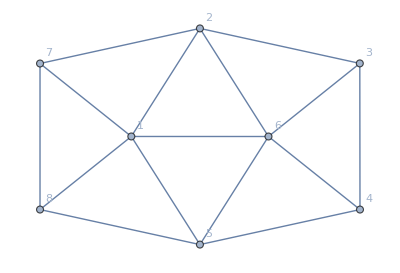

```mathematica
allGraphs=Association[];
g=Graph[Range[TheSize],{1<->2,2<->3,3<->4,4<->5,5<->1,6<->1,6<->2,6<->3,6<->4,6<->5,2<->7,7<->8,8<->5,1<->7,1<->8}];
Graph[g,VertexLabels->"Name"]
```

```mathematica
mat = MatrixFromGraph[g];MatrixForm[mat]
```

(2 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 2 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 2 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 2 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 2 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 2)

```mathematica
FileName="d:\\Saved\\allGraphsDoubleP.m";
If[FileExistsQ[FileName],
Print["Loading ... ", FileName];
allGraphs=Get[FileName],
Timing[Monitor[ComputeGraph[mat,32],{globalDepth,Length[allGraphs]}]];
Put[allGraphs,FileName]
];
Length[allGraphs]
```

Loading ... d:\Saved\allGraphsDoubleP.m

11687

```mathematica
ContractNodes[matrix_,x_,y_]:=Block[{result=matrix,size=Length[matrix],i,max},
For[i=1,i≤size,i++,
max=Max[result[[i,x]],result[[i,y]]];
result[[i,x]]=max;
result[[x,i]]=max;
result[[i,y]]=max;
result[[y,i]]=max;
];
result
]
```

```mathematica
ContractNodes[matrix_,set_]:=Block[{result=matrix,size=Length[matrix],i,max},
For[i=1,i≤size,i++,
max=Max[Table[result[[i,current]],{current,set}]];
Table[
result[[i,current]]=max;
result[[current,i]]=max
,{current,set}];
];
result
]
```

```mathematica
Monitor[
Table[
With[{
mat2=ContractNodes[mat,nodes]
},
Print[Timing[Monitor[ComputeGraph[mat2,32],{globalDepth,Length[allGraphs]}]]];
With[{key=GraphMatrixSignature[mat2]},
allGraphs[key,"comp"]=Greater;
allGraphs[key,"compwhy"]="derived from 5-node problem"
]
]
,
{nodes,{{7,8},{8,5},{5,4},{4,3},{3,2},{2,7}}}
],
nodes]
```

{144.641,8047690274306}

{139.438,8047675926157}

{140.641,8894966149495}

{136.625,8048844564076}

{140.516,10594190976661}

{141.359,8047733498101}

{derived from 5-node problem,derived from 5-node problem,derived from 5-node problem,derived from 5-node problem,derived from 5-node problem,derived from 5-node problem}

## Propagate ..

```mathematica
PropagateAllGraphs[]
```

The relation holds x11439556835482== x11439558429805(Equal) + 11439560083258 (Equal) (zero propagated)

The relation holds x11439556835482== x11439556894531(Equal) + 11439558547906 (Equal) (zero propagated)

The relation holds x11439556835482== x11439556835563(Equal) + 11439558429976 (Equal) (zero propagated)

The relation holds x11439556835482== x11439556835491(Equal) + 11439556835584 (Equal) (zero propagated)

The relation holds x11439556835482== x11439556835485(Equal) + 11439556894546 (Equal) (zero propagated)

The relation holds x11437232309632== x11438394571099(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11437232309632== x11437233903955(Equal) + 11437235557408 (Equal) (zero propagated)

The relation holds x11437232309632== x11437232368681(Equal) + 11437234022785 (Equal) (zero propagated)

The relation holds x11437232309632== x11437232309713(Equal) + 11437233906313 (Equal) (zero propagated)

The relation holds x11437232309632== x11437232309641(Equal) + 11437232311921 (Equal) (zero propagated)

The relation holds x11437232309632== x11437232309635(Equal) + 11437232369425 (Equal) (zero propagated)

The relation holds x11437232311819== x11438394573286(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11437232311819== x11437233906142(Equal) + 11437235559595 (Equal) (zero propagated)

The relation holds x11437232311819== x11437232370868(Equal) + 11437234024972 (Equal) (zero propagated)

The relation holds x11437232311819== x11437232311900(Equal) + 11437233906313 (Equal) (zero propagated)

The relation holds x11437232311819== x11437232311828(Equal) + 11437232311921 (Equal) (zero propagated)

The relation holds x11437232311819== x11437232311822(Equal) + 11437232371612 (Equal) (zero propagated)

The relation holds x11437232312548== x11438394574015(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11437232312548== x11437233906871(Equal) + 11437235560324 (Equal) (zero propagated)

The relation holds x11437232312548== x11437232371597(Equal) + 11437234024972 (Equal) (zero propagated)

The relation holds x11437232312548== x11437232312629(Equal) + 11437233907042 (Equal) (zero propagated)

The relation holds x11437232312548== x11437232312557(Equal) + 11437232312650 (Equal) (zero propagated)

The relation holds x11437232312548== x11437232312551(Equal) + 11437232371612 (Equal) (zero propagated)

The relation holds x11437232310361== x11438394571828(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11437232310361== x11437233904684(Equal) + 11437235558137 (Equal) (zero propagated)

The relation holds x11437232310361== x11437232369410(Equal) + 11437234022785 (Equal) (zero propagated)

The relation holds x11437232310361== x11437232312548(Equal) + 11438394576292 (Equal) (zero propagated)

The relation holds x11437232310361== x11437232310442(Equal) + 11437233907042 (Equal) (zero propagated)

The relation holds x11437232310361== x11437232310370(Equal) + 11437232312650 (Equal) (zero propagated)

The relation holds x11437232310361== x11437232310364(Equal) + 11437232369425 (Equal) (zero propagated)

The relation holds x11437221209230== x11438383470697(Equal) + 11439560083258 (Equal) (zero propagated)

The relation holds x11437221209230== x11437235558137(Equal) + 11438412168514 (Equal) (zero propagated)

The relation holds x11437221209230== x11437221211417(Equal) + 11438383475080 (Equal) (zero propagated)

The relation holds x11437221209230== x11437221209239(Equal) + 11437221211438 (Equal) (zero propagated)

The relation holds x11437221209230== x11437221209233(Equal) + 11437235558152 (Equal) (zero propagated)

The relation holds x11437218020503== x11438380281970(Equal) + 11439556894531 (Equal) (zero propagated)

The relation holds x11437218020503== x11437232369410(Equal) + 11438408979787 (Equal) (zero propagated)

The relation holds x11437218020503== x11437219614826(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11437218020503== x11437218022690(Equal) + 11438380286434 (Equal) (zero propagated)

The relation holds x11437218020503== x11437218020512(Equal) + 11437218022792 (Equal) (zero propagated)

The relation holds x11437218020503== x11437218020506(Equal) + 11437232369425 (Equal) (zero propagated)

The relation holds x11437218020584== x11438380282051(Equal) + 11439556894612 (Equal) (zero propagated)

The relation holds x11437218020584== x11437232369491(Equal) + 11438408979868 (Equal) (zero propagated)

The relation holds x11437218020584== x11437219614907(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11437218020584== x11437218022771(Equal) + 11438380286434 (Equal) (zero propagated)

The relation holds x11437218020584== x11437218020593(Equal) + 11437218022792 (Equal) (zero propagated)

The relation holds x11437218020584== x11437218020587(Equal) + 11437232369506 (Equal) (zero propagated)

The relation holds x11437217963641== x11438380225108(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11437217963641== x11437232312548(Equal) + 11438408981974 (Equal) (zero propagated)

The relation holds x11437217963641== x11437219557964(Equal) + 11437221211417 (Equal) (zero propagated)

The relation holds x11437217963641== x11437218022690(Equal) + 11437234024972 (Equal) (zero propagated)

The relation holds x11437217963641== x11437217963722(Equal) + 11437219558135 (Equal) (zero propagated)

The relation holds x11437217963641== x11437217963650(Equal) + 11437217963743 (Equal) (zero propagated)

The relation holds x11437217963641== x11437217963644(Equal) + 11437232371612 (Equal) (zero propagated)

The relation holds x11437217961454== x11438380222921(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11437217961454== x11437232310361(Equal) + 11438408979787 (Equal) (zero propagated)

The relation holds x11437217961454== x11437219555777(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11437217961454== x11437218020503(Equal) + 11437234022785 (Equal) (zero propagated)

The relation holds x11437217961454== x11437217963641(Equal) + 11438380227385 (Equal) (zero propagated)

The relation holds x11437217961454== x11437217961463(Equal) + 11437217963743 (Equal) (zero propagated)

The relation holds x11437217961454== x11437217961457(Equal) + 11437232369425 (Equal) (zero propagated)

The relation holds x11437217961535== x11438380223002(Equal) + 11439556835563 (Equal) (zero propagated)

The relation holds x11437217961535== x11437232310442(Equal) + 11438408979868 (Equal) (zero propagated)

The relation holds x11437217961535== x11437219555858(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11437217961535== x11437218020584(Equal) + 11437234022866 (Equal) (zero propagated)

The relation holds x11437217961535== x11437217963722(Equal) + 11438380227385 (Equal) (zero propagated)

The relation holds x11437217961535== x11437217961544(Equal) + 11437217963743 (Equal) (zero propagated)

The relation holds x11437217961535== x11437217961538(Equal) + 11437232369506 (Equal) (zero propagated)

The relation holds x11437217843437== x11438380104904(Equal) + 11439556717465 (Equal) (zero propagated)

The relation holds x11437217843437== x11437232192344(Equal) + 11438408802721 (Equal) (zero propagated)

The relation holds x11437217843437== x11437219437760(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11437217843437== x11437218020584(Equal) + 11437219794250 (Equal) (zero propagated)

The relation holds x11437217843437== x11437217845624(Equal) + 11438380286434 (Equal) (zero propagated)

The relation holds x11437217843437== x11437217843446(Equal) + 11437218022792 (Equal) (zero propagated)

The relation holds x11437217843437== x11437217843440(Equal) + 11437232192359 (Equal) (zero propagated)

The relation holds x11437217784388== x11438380045855(Equal) + 11439556658416 (Equal) (zero propagated)

The relation holds x11437217784388== x11437232133295(Equal) + 11438408802721 (Equal) (zero propagated)

The relation holds x11437217784388== x11437219378711(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11437217784388== x11437217961535(Equal) + 11437219794250 (Equal) (zero propagated)

The relation holds x11437217784388== x11437217843437(Equal) + 11437234022866 (Equal) (zero propagated)

The relation holds x11437217784388== x11437217786575(Equal) + 11438380227385 (Equal) (zero propagated)

The relation holds x11437217784388== x11437217784397(Equal) + 11437217963743 (Equal) (zero propagated)

The relation holds x11437217784388== x11437217784391(Equal) + 11437232192359 (Equal) (zero propagated)

The relation holds x11436844889143== x11438007150610(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11436844889143== x11437232309632(Equal) + 11438783585992 (Equal) (zero propagated)

The relation holds x11436844889143== x11436846483466(Equal) + 11437235557408 (Equal) (zero propagated)

The relation holds x11436844889143== x11436844948192(Equal) + 11436846602296 (Equal) (zero propagated)

The relation holds x11436844891330== x11438007152797(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11436844891330== x11437232311819(Equal) + 11438783588179 (Equal) (zero propagated)

The relation holds x11436844891330== x11436846485653(Equal) + 11437235559595 (Equal) (zero propagated)

The relation holds x11436844891330== x11436844950379(Equal) + 11436846604483 (Equal) (zero propagated)

The relation holds x11436844892059== x11438007153526(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11436844892059== x11437232312548(Equal) + 11438783588908 (Equal) (zero propagated)

The relation holds x11436844892059== x11436846486382(Equal) + 11437235560324 (Equal) (zero propagated)

The relation holds x11436844892059== x11436844951108(Equal) + 11436846604483 (Equal) (zero propagated)

The relation holds x11436844892059== x11436844892140(Equal) + 11437233907042 (Equal) (zero propagated)

The relation holds x11436844892059== x11436844892068(Equal) + 11436844892161 (Equal) (zero propagated)

The relation holds x11436844892059== x11436844892062(Equal) + 11436844951123 (Equal) (zero propagated)

The relation holds x11436844891411== x11438007152878(Equal) + 11439556835563 (Equal) (zero propagated)

The relation holds x11436844891411== x11437232311900(Equal) + 11438783588179 (Equal) (zero propagated)

The relation holds x11436844891411== x11436846485734(Equal) + 11437235559595 (Equal) (zero propagated)

The relation holds x11436844891411== x11436844950460(Equal) + 11436846604564 (Equal) (zero propagated)

The relation holds x11436844891411== x11436844892140(Equal) + 11438007213388 (Equal) (zero propagated)

The relation holds x11436844891432== x11438007152899(Equal) + 11439556835584 (Equal) (zero propagated)

The relation holds x11436844891432== x11437232311921(Equal) + 11438783588200 (Equal) (zero propagated)

The relation holds x11436844891432== x11436846485755(Equal) + 11437235559616 (Equal) (zero propagated)

The relation holds x11436844891432== x11436844950481(Equal) + 11436846604582 (Equal) (zero propagated)

The relation holds x11436844891432== x11436844892161(Equal) + 11438007213406 (Equal) (zero propagated)

The relation holds x11436844891414== x11438007152881(Equal) + 11439556835566 (Equal) (zero propagated)

The relation holds x11436844891414== x11437232311903(Equal) + 11438783588182 (Equal) (zero propagated)

The relation holds x11436844891414== x11436846485737(Equal) + 11437235559598 (Equal) (zero propagated)

The relation holds x11436844891414== x11436844950463(Equal) + 11436846604564 (Equal) (zero propagated)

The relation holds x11436844891414== x11436844892143(Equal) + 11438007213388 (Equal) (zero propagated)

The relation holds x11436844891414== x11436844891423(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844891333== x11438007152800(Equal) + 11439556835485 (Equal) (zero propagated)

The relation holds x11436844891333== x11437232311822(Equal) + 11438783588182 (Equal) (zero propagated)

The relation holds x11436844891333== x11436846485656(Equal) + 11437235559598 (Equal) (zero propagated)

The relation holds x11436844891333== x11436844950382(Equal) + 11436846604483 (Equal) (zero propagated)

The relation holds x11436844891333== x11436844892062(Equal) + 11438007213307 (Equal) (zero propagated)

The relation holds x11436844891333== x11436844891414(Equal) + 11437233906316 (Equal) (zero propagated)

The relation holds x11436844891333== x11436844891342(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844889872== x11438007151339(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11436844889872== x11437232310361(Equal) + 11438783586721 (Equal) (zero propagated)

The relation holds x11436844889872== x11436846484195(Equal) + 11437235558137 (Equal) (zero propagated)

The relation holds x11436844889872== x11436844948921(Equal) + 11436846602296 (Equal) (zero propagated)

The relation holds x11436844889872== x11436844892059(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844889872== x11436844889881(Equal) + 11436844892161 (Equal) (zero propagated)

The relation holds x11436844889872== x11436844889875(Equal) + 11436844948936 (Equal) (zero propagated)

The relation holds x11436844889953== x11438007151420(Equal) + 11439556835563 (Equal) (zero propagated)

The relation holds x11436844889953== x11437232310442(Equal) + 11438783586721 (Equal) (zero propagated)

The relation holds x11436844889953== x11436846484276(Equal) + 11437235558137 (Equal) (zero propagated)

The relation holds x11436844889953== x11436844949002(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436844889953== x11436844892140(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844889953== x11436844889962(Equal) + 11436844892161 (Equal) (zero propagated)

The relation holds x11436844889953== x11436844889956(Equal) + 11436844949017 (Equal) (zero propagated)

The relation holds x11436844889224== x11438007150691(Equal) + 11439556835563 (Equal) (zero propagated)

The relation holds x11436844889224== x11437232309713(Equal) + 11438783585992 (Equal) (zero propagated)

The relation holds x11436844889224== x11436846483547(Equal) + 11437235557408 (Equal) (zero propagated)

The relation holds x11436844889224== x11436844948273(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436844889224== x11436844891411(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844889224== x11436844889953(Equal) + 11438007213388 (Equal) (zero propagated)

The relation holds x11436844889224== x11436844889233(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844889227== x11438007150694(Equal) + 11439556835566 (Equal) (zero propagated)

The relation holds x11436844889227== x11437232309716(Equal) + 11438783585995 (Equal) (zero propagated)

The relation holds x11436844889227== x11436846483550(Equal) + 11437235557411 (Equal) (zero propagated)

The relation holds x11436844889227== x11436844948276(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436844889227== x11436844891414(Equal) + 11438007155806 (Equal) (zero propagated)

The relation holds x11436844889227== x11436844889956(Equal) + 11438007213388 (Equal) (zero propagated)

The relation holds x11436844889227== x11436844889236(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844889146== x11438007150613(Equal) + 11439556835485 (Equal) (zero propagated)

The relation holds x11436844889146== x11437232309635(Equal) + 11438783585995 (Equal) (zero propagated)

The relation holds x11436844889146== x11436846483469(Equal) + 11437235557411 (Equal) (zero propagated)

The relation holds x11436844889146== x11436844948195(Equal) + 11436846602296 (Equal) (zero propagated)

The relation holds x11436844889146== x11436844891333(Equal) + 11438007155806 (Equal) (zero propagated)

The relation holds x11436844889146== x11436844889875(Equal) + 11438007213307 (Equal) (zero propagated)

The relation holds x11436844889146== x11436844889227(Equal) + 11437233906316 (Equal) (zero propagated)

The relation holds x11436844889146== x11436844889155(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844773313== x11438007034780(Equal) + 11439556717465 (Equal) (zero propagated)

The relation holds x11436844773313== x11437232193802(Equal) + 11438783470081 (Equal) (zero propagated)

The relation holds x11436844773313== x11436846367636(Equal) + 11437235559595 (Equal) (zero propagated)

The relation holds x11436844773313== x11436844950460(Equal) + 11436846721939 (Equal) (zero propagated)

The relation holds x11436844773313== x11436844774042(Equal) + 11438007036241 (Equal) (zero propagated)

The relation holds x11436844773313== x11436844773322(Equal) + 11436844950481 (Equal) (zero propagated)

The relation holds x11436844773313== x11436844773316(Equal) + 11436844774057 (Equal) (zero propagated)

The relation holds x11436844771855== x11438007033322(Equal) + 11439556717465 (Equal) (zero propagated)

The relation holds x11436844771855== x11437232192344(Equal) + 11438783468623 (Equal) (zero propagated)

The relation holds x11436844771855== x11436846366178(Equal) + 11437235558137 (Equal) (zero propagated)

The relation holds x11436844771855== x11436844949002(Equal) + 11436846722668 (Equal) (zero propagated)

The relation holds x11436844771855== x11436844774042(Equal) + 11438007214852 (Equal) (zero propagated)

The relation holds x11436844771864== x11438007033331(Equal) + 11439556717474 (Equal) (zero propagated)

The relation holds x11436844771864== x11437232192353(Equal) + 11438783468632 (Equal) (zero propagated)

The relation holds x11436844771864== x11436846366187(Equal) + 11437235558146 (Equal) (zero propagated)

The relation holds x11436844771864== x11436844949011(Equal) + 11436846722668 (Equal) (zero propagated)

The relation holds x11436844771864== x11436844774051(Equal) + 11438007214852 (Equal) (zero propagated)

The relation holds x11436844771870== x11438007033337(Equal) + 11439556717480 (Equal) (zero propagated)

The relation holds x11436844771870== x11437232192359(Equal) + 11438783468638 (Equal) (zero propagated)

The relation holds x11436844771870== x11436846366193(Equal) + 11437235558152 (Equal) (zero propagated)

The relation holds x11436844771870== x11436844949017(Equal) + 11436846722674 (Equal) (zero propagated)

The relation holds x11436844771870== x11436844774057(Equal) + 11438007214858 (Equal) (zero propagated)

The relation holds x11436844771126== x11438007032593(Equal) + 11439556717465 (Equal) (zero propagated)

The relation holds x11436844771126== x11437232191615(Equal) + 11438783467894 (Equal) (zero propagated)

The relation holds x11436844771126== x11436846365449(Equal) + 11437235557408 (Equal) (zero propagated)

The relation holds x11436844771126== x11436844948273(Equal) + 11436846721939 (Equal) (zero propagated)

The relation holds x11436844771126== x11436844773313(Equal) + 11438007214852 (Equal) (zero propagated)

The relation holds x11436844771126== x11436844771855(Equal) + 11438007036241 (Equal) (zero propagated)

The relation holds x11436844771126== x11436844771129(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436844771135== x11438007032602(Equal) + 11439556717474 (Equal) (zero propagated)

The relation holds x11436844771135== x11437232191624(Equal) + 11438783467903 (Equal) (zero propagated)

The relation holds x11436844771135== x11436846365458(Equal) + 11437235557417 (Equal) (zero propagated)

The relation holds x11436844771135== x11436844948282(Equal) + 11436846721939 (Equal) (zero propagated)

The relation holds x11436844771135== x11436844773322(Equal) + 11438007214852 (Equal) (zero propagated)

The relation holds x11436844771135== x11436844771864(Equal) + 11438007036250 (Equal) (zero propagated)

The relation holds x11436844771135== x11436844771138(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436844714264== x11438006975731(Equal) + 11439556658416 (Equal) (zero propagated)

The relation holds x11436844714264== x11437232134753(Equal) + 11438783411032 (Equal) (zero propagated)

The relation holds x11436844714264== x11436846308587(Equal) + 11437235559595 (Equal) (zero propagated)

The relation holds x11436844714264== x11436844891411(Equal) + 11436846721939 (Equal) (zero propagated)

The relation holds x11436844714264== x11436844773313(Equal) + 11436846604564 (Equal) (zero propagated)

The relation holds x11436844714264== x11436844714993(Equal) + 11438007036241 (Equal) (zero propagated)

The relation holds x11436844714264== x11436844714273(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844714267== x11438006975734(Equal) + 11439556658419 (Equal) (zero propagated)

The relation holds x11436844714267== x11437232134756(Equal) + 11438783411035 (Equal) (zero propagated)

The relation holds x11436844714267== x11436846308590(Equal) + 11437235559598 (Equal) (zero propagated)

The relation holds x11436844714267== x11436844891414(Equal) + 11436846721942 (Equal) (zero propagated)

The relation holds x11436844714267== x11436844773316(Equal) + 11436846604564 (Equal) (zero propagated)

The relation holds x11436844714267== x11436844714996(Equal) + 11438007036241 (Equal) (zero propagated)

The relation holds x11436844714267== x11436844714276(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844714186== x11438006975653(Equal) + 11439556658338 (Equal) (zero propagated)

The relation holds x11436844714186== x11437232134675(Equal) + 11438783411035 (Equal) (zero propagated)

The relation holds x11436844714186== x11436846308509(Equal) + 11437235382370 (Equal) (zero propagated)

The relation holds x11436844714186== x11436844891333(Equal) + 11436845127538 (Equal) (zero propagated)

The relation holds x11436844714186== x11436844773235(Equal) + 11436846604483 (Equal) (zero propagated)

The relation holds x11436844714186== x11436844714915(Equal) + 11438007036160 (Equal) (zero propagated)

The relation holds x11436844714186== x11436844714267(Equal) + 11437232134846 (Equal) (zero propagated)

The relation holds x11436844714186== x11436844714195(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844712806== x11438006974273(Equal) + 11439556658416 (Equal) (zero propagated)

The relation holds x11436844712806== x11437232133295(Equal) + 11438783409574 (Equal) (zero propagated)

The relation holds x11436844712806== x11436846307129(Equal) + 11437235558137 (Equal) (zero propagated)

The relation holds x11436844712806== x11436844889953(Equal) + 11436846722668 (Equal) (zero propagated)

The relation holds x11436844712806== x11436844771855(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436844712806== x11436844714993(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844712806== x11436844712809(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436844712815== x11438006974282(Equal) + 11439556658425 (Equal) (zero propagated)

The relation holds x11436844712815== x11437232133304(Equal) + 11438783409583 (Equal) (zero propagated)

The relation holds x11436844712815== x11436846307138(Equal) + 11437235558146 (Equal) (zero propagated)

The relation holds x11436844712815== x11436844889962(Equal) + 11436846722668 (Equal) (zero propagated)

The relation holds x11436844712815== x11436844771864(Equal) + 11436846602386 (Equal) (zero propagated)

The relation holds x11436844712815== x11436844715002(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844712815== x11436844712818(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436844712077== x11438006973544(Equal) + 11439556658416 (Equal) (zero propagated)

The relation holds x11436844712077== x11437232132566(Equal) + 11438783408845 (Equal) (zero propagated)

The relation holds x11436844712077== x11436846306400(Equal) + 11437235557408 (Equal) (zero propagated)

The relation holds x11436844712077== x11436844889224(Equal) + 11436846721939 (Equal) (zero propagated)

The relation holds x11436844712077== x11436844771126(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436844712077== x11436844714264(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844712077== x11436844712806(Equal) + 11438007036241 (Equal) (zero propagated)

The relation holds x11436844712086== x11438006973553(Equal) + 11439556658425 (Equal) (zero propagated)

The relation holds x11436844712086== x11437232132575(Equal) + 11438783408854 (Equal) (zero propagated)

The relation holds x11436844712086== x11436846306409(Equal) + 11437235557417 (Equal) (zero propagated)

The relation holds x11436844712086== x11436844889233(Equal) + 11436846721939 (Equal) (zero propagated)

The relation holds x11436844712086== x11436844771135(Equal) + 11436846602386 (Equal) (zero propagated)

The relation holds x11436844712086== x11436844714273(Equal) + 11438007155803 (Equal) (zero propagated)

The relation holds x11436844712086== x11436844712815(Equal) + 11438007036250 (Equal) (zero propagated)

The relation holds x11436844712086== x11436844712089(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436844712080== x11438006973547(Equal) + 11439556658419 (Equal) (zero propagated)

The relation holds x11436844712080== x11437232132569(Equal) + 11438783408848 (Equal) (zero propagated)

The relation holds x11436844712080== x11436846306403(Equal) + 11437235557411 (Equal) (zero propagated)

The relation holds x11436844712080== x11436844889227(Equal) + 11436846721942 (Equal) (zero propagated)

The relation holds x11436844712080== x11436844771129(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436844712080== x11436844714267(Equal) + 11438007155806 (Equal) (zero propagated)

The relation holds x11436844712080== x11436844712809(Equal) + 11438007036241 (Equal) (zero propagated)

The relation holds x11436844712080== x11436844712089(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436844711999== x11438006973466(Equal) + 11439556658338 (Equal) (zero propagated)

The relation holds x11436844711999== x11437232132488(Equal) + 11438783408848 (Equal) (zero propagated)

The relation holds x11436844711999== x11436846306322(Equal) + 11437235380183 (Equal) (zero propagated)

The relation holds x11436844711999== x11436844889146(Equal) + 11436845127538 (Equal) (zero propagated)

The relation holds x11436844711999== x11436844771048(Equal) + 11436846602296 (Equal) (zero propagated)

The relation holds x11436844711999== x11436844714186(Equal) + 11438007155806 (Equal) (zero propagated)

The relation holds x11436844711999== x11436844712728(Equal) + 11438007036160 (Equal) (zero propagated)

The relation holds x11436844711999== x11436844712080(Equal) + 11437232134846 (Equal) (zero propagated)

The relation holds x11436844711999== x11436844712008(Equal) + 11436844891432 (Equal) (zero propagated)

The relation holds x11436830600014== x11437992861481(Equal) + 11439556894531 (Equal) (zero propagated)

The relation holds x11436830600014== x11437218020503(Equal) + 11438783645770 (Equal) (zero propagated)

The relation holds x11436830600014== x11436844948921(Equal) + 11438408979787 (Equal) (zero propagated)

The relation holds x11436830600014== x11436832194337(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11436830600014== x11436830602201(Equal) + 11437992865945 (Equal) (zero propagated)

The relation holds x11436830600014== x11436830600023(Equal) + 11436830602303 (Equal) (zero propagated)

The relation holds x11436830600014== x11436830600017(Equal) + 11436844948936 (Equal) (zero propagated)

The relation holds x11436830600095== x11437992861562(Equal) + 11439556894612 (Equal) (zero propagated)

The relation holds x11436830600095== x11437218020584(Equal) + 11438783645770 (Equal) (zero propagated)

The relation holds x11436830600095== x11436844949002(Equal) + 11438408979868 (Equal) (zero propagated)

The relation holds x11436830600095== x11436832194418(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11436830600095== x11436830602282(Equal) + 11437992865945 (Equal) (zero propagated)

The relation holds x11436830600095== x11436830600104(Equal) + 11436830602303 (Equal) (zero propagated)

The relation holds x11436830600095== x11436830600098(Equal) + 11436844949017 (Equal) (zero propagated)

The relation holds x11436830543152== x11437992804619(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11436830543152== x11437217963641(Equal) + 11438783588908 (Equal) (zero propagated)

The relation holds x11436830543152== x11436844892059(Equal) + 11438408981974 (Equal) (zero propagated)

The relation holds x11436830543152== x11436832137475(Equal) + 11437221211417 (Equal) (zero propagated)

The relation holds x11436830543152== x11436830602201(Equal) + 11436846604483 (Equal) (zero propagated)

The relation holds x11436830543152== x11436830543233(Equal) + 11437219558135 (Equal) (zero propagated)

The relation holds x11436830543152== x11436830543161(Equal) + 11436830543254 (Equal) (zero propagated)

The relation holds x11436830543152== x11436830543155(Equal) + 11436844951123 (Equal) (zero propagated)

The relation holds x11436830540965== x11437992802432(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x11436830540965== x11437217961454(Equal) + 11438783586721 (Equal) (zero propagated)

The relation holds x11436830540965== x11436844889872(Equal) + 11438408979787 (Equal) (zero propagated)

The relation holds x11436830540965== x11436832135288(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11436830540965== x11436830600014(Equal) + 11436846602296 (Equal) (zero propagated)

The relation holds x11436830540965== x11436830543152(Equal) + 11437992806896 (Equal) (zero propagated)

The relation holds x11436830540965== x11436830540974(Equal) + 11436830543254 (Equal) (zero propagated)

The relation holds x11436830540965== x11436830540968(Equal) + 11436844948936 (Equal) (zero propagated)

The relation holds x11436830541046== x11437992802513(Equal) + 11439556835563 (Equal) (zero propagated)

The relation holds x11436830541046== x11437217961535(Equal) + 11438783586721 (Equal) (zero propagated)

The relation holds x11436830541046== x11436844889953(Equal) + 11438408979868 (Equal) (zero propagated)

The relation holds x11436830541046== x11436832135369(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11436830541046== x11436830600095(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436830541046== x11436830543233(Equal) + 11437992806896 (Equal) (zero propagated)

The relation holds x11436830541046== x11436830541055(Equal) + 11436830543254 (Equal) (zero propagated)

The relation holds x11436830541046== x11436830541049(Equal) + 11436844949017 (Equal) (zero propagated)

The relation holds x11436830422948== x11437992684415(Equal) + 11439556717465 (Equal) (zero propagated)

The relation holds x11436830422948== x11437217843437(Equal) + 11438783468623 (Equal) (zero propagated)

The relation holds x11436830422948== x11436844771855(Equal) + 11438408802721 (Equal) (zero propagated)

The relation holds x11436830422948== x11436832017271(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11436830422948== x11436830600095(Equal) + 11436832373761 (Equal) (zero propagated)

The relation holds x11436830422948== x11436830425135(Equal) + 11437992865945 (Equal) (zero propagated)

The relation holds x11436830422948== x11436830422951(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436830422957== x11437992684424(Equal) + 11439556717474 (Equal) (zero propagated)

The relation holds x11436830422957== x11437217843446(Equal) + 11438783468632 (Equal) (zero propagated)

The relation holds x11436830422957== x11436844771864(Equal) + 11438408802730 (Equal) (zero propagated)

The relation holds x11436830422957== x11436832017280(Equal) + 11437221209239 (Equal) (zero propagated)

The relation holds x11436830422957== x11436830600104(Equal) + 11436832373761 (Equal) (zero propagated)

The relation holds x11436830422957== x11436830425144(Equal) + 11437992865945 (Equal) (zero propagated)

The relation holds x11436830422957== x11436830422960(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436830422228== x11437992683695(Equal) + 11439542367838 (Equal) (zero propagated)

The relation holds x11436830422228== x11437217842717(Equal) + 11438783467903 (Equal) (zero propagated)

The relation holds x11436830422228== x11436844771135(Equal) + 11437246540534 (Equal) (zero propagated)

The relation holds x11436830422228== x11436832016551(Equal) + 11437221208510 (Equal) (zero propagated)

The relation holds x11436830422228== x11436830599375(Equal) + 11436832373032 (Equal) (zero propagated)

The relation holds x11436830422228== x11436830424415(Equal) + 11437992865945 (Equal) (zero propagated)

The relation holds x11436830422228== x11436830422957(Equal) + 11436830425876 (Equal) (zero propagated)

The relation holds x11436830422228== x11436830422231(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436830363899== x11437992625366(Equal) + 11439556658416 (Equal) (zero propagated)

The relation holds x11436830363899== x11437217784388(Equal) + 11438783409574 (Equal) (zero propagated)

The relation holds x11436830363899== x11436844712806(Equal) + 11438408802721 (Equal) (zero propagated)

The relation holds x11436830363899== x11436831958222(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x11436830363899== x11436830541046(Equal) + 11436832373761 (Equal) (zero propagated)

The relation holds x11436830363899== x11436830422948(Equal) + 11436846602377 (Equal) (zero propagated)

The relation holds x11436830363899== x11436830366086(Equal) + 11437992806896 (Equal) (zero propagated)

The relation holds x11436830363899== x11436830363902(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436830363908== x11437992625375(Equal) + 11439556658425 (Equal) (zero propagated)

The relation holds x11436830363908== x11437217784397(Equal) + 11438783409583 (Equal) (zero propagated)

The relation holds x11436830363908== x11436844712815(Equal) + 11438408802730 (Equal) (zero propagated)

The relation holds x11436830363908== x11436831958231(Equal) + 11437221209239 (Equal) (zero propagated)

The relation holds x11436830363908== x11436830541055(Equal) + 11436832373761 (Equal) (zero propagated)

The relation holds x11436830363908== x11436830422957(Equal) + 11436846602386 (Equal) (zero propagated)

The relation holds x11436830363908== x11436830366095(Equal) + 11437992806896 (Equal) (zero propagated)

The relation holds x11436830363908== x11436830363911(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x11436830363179== x11437992624646(Equal) + 11439542308789 (Equal) (zero propagated)

The relation holds x11436830363179== x11437217783668(Equal) + 11438783408854 (Equal) (zero propagated)

The relation holds x11436830363179== x11436844712086(Equal) + 11437246540534 (Equal) (zero propagated)

The relation holds x11436830363179== x11436831957502(Equal) + 11437221208510 (Equal) (zero propagated)

The relation holds x11436830363179== x11436830540326(Equal) + 11436832373032 (Equal) (zero propagated)

The relation holds x11436830363179== x11436830422228(Equal) + 11436846602386 (Equal) (zero propagated)

The relation holds x11436830363179== x11436830365366(Equal) + 11437992806896 (Equal) (zero propagated)

The relation holds x11436830363179== x11436830363908(Equal) + 11436830425876 (Equal) (zero propagated)

The relation holds x11436830363179== x11436830363182(Equal) + 11436844771870 (Equal) (zero propagated)

The relation holds x12285683183458== x12285684777781(Equal) + 12285686431234 (Equal) (zero propagated)

The relation holds x12285683183458== x12285683242507(Equal) + 12285684895882 (Equal) (zero propagated)

The relation holds x12285683183458== x12285683183539(Equal) + 12285684777952 (Equal) (zero propagated)

The relation holds x12285683183458== x12285683183467(Equal) + 12285683183560 (Equal) (zero propagated)

The relation holds x12285683183458== x12285683183461(Equal) + 12285683242522 (Equal) (zero propagated)

The relation holds x12285283067434== x12285670487923(Equal) + 12286072257400 (Equal) (zero propagated)

The relation holds x12285283067434== x12285297416341(Equal) + 12285699185740 (Equal) (zero propagated)

The relation holds x12285283067434== x12285283067515(Equal) + 12285670488094 (Equal) (zero propagated)

The relation holds x12285283067434== x12285283067443(Equal) + 12285283067536 (Equal) (zero propagated)

The relation holds x12285283067434== x12285283067437(Equal) + 12285297416356 (Equal) (zero propagated)

The relation holds x12285282831250== x12285670251739(Equal) + 12286072021216 (Equal) (zero propagated)

The relation holds x12285282831250== x12285297180157(Equal) + 12285699008602 (Equal) (zero propagated)

The relation holds x12285282831250== x12285283008397(Equal) + 12285283244674 (Equal) (zero propagated)

The relation holds x12285282831250== x12285282890299(Equal) + 12285297475402 (Equal) (zero propagated)

The relation holds x12285282831250== x12285282831331(Equal) + 12285670429048 (Equal) (zero propagated)

The relation holds x10591105961656== x11438394571099(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10591105961656== x10591107555979(Equal) + 10591109209432 (Equal) (zero propagated)

The relation holds x10591105961656== x10591106020705(Equal) + 10591107674809 (Equal) (zero propagated)

The relation holds x10591105961656== x10591105961737(Equal) + 10591107558337 (Equal) (zero propagated)

The relation holds x10591105961656== x10591105961665(Equal) + 10591105963945 (Equal) (zero propagated)

The relation holds x10591105961656== x10591105961659(Equal) + 10591106021449 (Equal) (zero propagated)

The relation holds x10591105963843== x11438394573286(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10591105963843== x10591107558166(Equal) + 10591109211619 (Equal) (zero propagated)

The relation holds x10591105963843== x10591106022892(Equal) + 10591107676996 (Equal) (zero propagated)

The relation holds x10591105963843== x10591105963924(Equal) + 10591107558337 (Equal) (zero propagated)

The relation holds x10591105963843== x10591105963852(Equal) + 10591105963945 (Equal) (zero propagated)

The relation holds x10591105963843== x10591105963846(Equal) + 10591106023636 (Equal) (zero propagated)

The relation holds x10591105964572== x11438394574015(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10591105964572== x10591107558895(Equal) + 10591109212348 (Equal) (zero propagated)

The relation holds x10591105964572== x10591106023621(Equal) + 10591107676996 (Equal) (zero propagated)

The relation holds x10591105964572== x10591105964653(Equal) + 10591107559066 (Equal) (zero propagated)

The relation holds x10591105964572== x10591105964581(Equal) + 10591105964674 (Equal) (zero propagated)

The relation holds x10591105964572== x10591105964575(Equal) + 10591106023636 (Equal) (zero propagated)

The relation holds x10591105962385== x11438394571828(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10591105962385== x10591107556708(Equal) + 10591109210161 (Equal) (zero propagated)

The relation holds x10591105962385== x10591106021434(Equal) + 10591107674809 (Equal) (zero propagated)

The relation holds x10591105962385== x10591105964572(Equal) + 11438394576292 (Equal) (zero propagated)

The relation holds x10591105962385== x10591105962466(Equal) + 10591107559066 (Equal) (zero propagated)

The relation holds x10591105962385== x10591105962394(Equal) + 10591105964674 (Equal) (zero propagated)

The relation holds x10591105962385== x10591105962388(Equal) + 10591106021449 (Equal) (zero propagated)

The relation holds x10590705845632== x11437994455075(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10590705845632== x10591093266121(Equal) + 10591495035598 (Equal) (zero propagated)

The relation holds x10590705845632== x10590720194539(Equal) + 10591121964667 (Equal) (zero propagated)

The relation holds x10590705845632== x10590705845713(Equal) + 10591093268479 (Equal) (zero propagated)

The relation holds x10590705845632== x10590705845641(Equal) + 10590705847921 (Equal) (zero propagated)

The relation holds x10590705845632== x10590705845635(Equal) + 10590720195283 (Equal) (zero propagated)

The relation holds x10590705847819== x11437994457262(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10590705847819== x10591093268308(Equal) + 10591495037785 (Equal) (zero propagated)

The relation holds x10590705847819== x10590720196726(Equal) + 10591121966854 (Equal) (zero propagated)

The relation holds x10590705847819== x10590705847900(Equal) + 10591093268479 (Equal) (zero propagated)

The relation holds x10590705847819== x10590705847828(Equal) + 10590705847921 (Equal) (zero propagated)

The relation holds x10590705847819== x10590705847822(Equal) + 10590720197470 (Equal) (zero propagated)

The relation holds x10590705848548== x11437994457991(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10590705848548== x10591093269037(Equal) + 10591495038514 (Equal) (zero propagated)

The relation holds x10590705848548== x10590720197455(Equal) + 10591121966854 (Equal) (zero propagated)

The relation holds x10590705848548== x10590705848629(Equal) + 10591093269208 (Equal) (zero propagated)

The relation holds x10590705848548== x10590705848557(Equal) + 10590705848650 (Equal) (zero propagated)

The relation holds x10590705848548== x10590705848551(Equal) + 10590720197470 (Equal) (zero propagated)

The relation holds x10590705846361== x11437994455804(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10590705846361== x10591093266850(Equal) + 10591495036327 (Equal) (zero propagated)

The relation holds x10590705846361== x10590720195268(Equal) + 10591121964667 (Equal) (zero propagated)

The relation holds x10590705846361== x10590705848548(Equal) + 11437994460268 (Equal) (zero propagated)

The relation holds x10590705846361== x10590705846442(Equal) + 10591093269208 (Equal) (zero propagated)

The relation holds x10590705846361== x10590705846370(Equal) + 10590705848650 (Equal) (zero propagated)

The relation holds x10590705846361== x10590705846364(Equal) + 10590720195283 (Equal) (zero propagated)

The relation holds x10590705612364== x11437994221807(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10590705612364== x10591093032853(Equal) + 10591494802330 (Equal) (zero propagated)

The relation holds x10590705612364== x10590719961271(Equal) + 10591121789716 (Equal) (zero propagated)

The relation holds x10590705612364== x10590705789511(Equal) + 10590706025788 (Equal) (zero propagated)

The relation holds x10590705612364== x10590705671413(Equal) + 10590720256516 (Equal) (zero propagated)

The relation holds x10590705612364== x10590705612445(Equal) + 10591093210162 (Equal) (zero propagated)

The relation holds x10590705611635== x11437994221078(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10590705611635== x10591093032124(Equal) + 10591494801601 (Equal) (zero propagated)

The relation holds x10590705611635== x10590719960542(Equal) + 10591121789716 (Equal) (zero propagated)

The relation holds x10590705611635== x10590705788782(Equal) + 10590706025059 (Equal) (zero propagated)

The relation holds x10590705611635== x10590705670684(Equal) + 10590720256516 (Equal) (zero propagated)

The relation holds x10590705611635== x10590705612364(Equal) + 11438008630492 (Equal) (zero propagated)

The relation holds x10590705611635== x10590705611716(Equal) + 10591093209433 (Equal) (zero propagated)

The relation holds x10590705610177== x11437994219620(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10590705610177== x10591093030666(Equal) + 10591494800143 (Equal) (zero propagated)

The relation holds x10590705610177== x10590719959084(Equal) + 10591121787529 (Equal) (zero propagated)

The relation holds x10590705610177== x10590705787324(Equal) + 10590706025788 (Equal) (zero propagated)

The relation holds x10590705610177== x10590705669226(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x10590705610177== x10590705612364(Equal) + 11437994401222 (Equal) (zero propagated)

The relation holds x10590705610177== x10590705610258(Equal) + 10591093210162 (Equal) (zero propagated)

The relation holds x10590705609448== x11437994218891(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10590705609448== x10591093029937(Equal) + 10591494799414 (Equal) (zero propagated)

The relation holds x10590705609448== x10590719958355(Equal) + 10591121787529 (Equal) (zero propagated)

The relation holds x10590705609448== x10590705786595(Equal) + 10590706025059 (Equal) (zero propagated)

The relation holds x10590705609448== x10590705668497(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x10590705609448== x10590705611635(Equal) + 11437994401222 (Equal) (zero propagated)

The relation holds x10590705609448== x10590705610177(Equal) + 11438008630492 (Equal) (zero propagated)

The relation holds x10590705609448== x10590705609529(Equal) + 10591093209433 (Equal) (zero propagated)

The relation holds x10589943700189== x11437232309632(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10589943700189== x10591105961656(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x10589943700189== x10589945294512(Equal) + 10589946947965 (Equal) (zero propagated)

The relation holds x10589943700189== x10589943759238(Equal) + 10589945413342 (Equal) (zero propagated)

The relation holds x10589943700189== x10589943700270(Equal) + 10589945296870 (Equal) (zero propagated)

The relation holds x10589943700189== x10589943700198(Equal) + 10589943702478 (Equal) (zero propagated)

The relation holds x10589943700189== x10589943700192(Equal) + 10589943759982 (Equal) (zero propagated)

The relation holds x10589943702376== x11437232311819(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10589943702376== x10591105963843(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x10589943702376== x10589945296699(Equal) + 10589946950152 (Equal) (zero propagated)

The relation holds x10589943702376== x10589943761425(Equal) + 10589945415529 (Equal) (zero propagated)

The relation holds x10589943702376== x10589943702457(Equal) + 10589945296870 (Equal) (zero propagated)

The relation holds x10589943702376== x10589943702385(Equal) + 10589943702478 (Equal) (zero propagated)

The relation holds x10589943702376== x10589943702379(Equal) + 10589943762169 (Equal) (zero propagated)

The relation holds x10589943703105== x11437232312548(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10589943703105== x10591105964572(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x10589943703105== x10589945297428(Equal) + 10589946950881 (Equal) (zero propagated)

The relation holds x10589943703105== x10589943762154(Equal) + 10589945415529 (Equal) (zero propagated)

The relation holds x10589943703105== x10589943703186(Equal) + 10589945297599 (Equal) (zero propagated)

The relation holds x10589943703105== x10589943703114(Equal) + 10589943703207 (Equal) (zero propagated)

The relation holds x10589943703105== x10589943703108(Equal) + 10589943762169 (Equal) (zero propagated)

The relation holds x10589943700918== x11437232310361(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x10589943700918== x10591105962385(Equal) + 11439556835482 (Equal) (zero propagated)

The relation holds x10589943700918== x10589945295241(Equal) + 10589946948694 (Equal) (zero propagated)

The relation holds x10589943700918== x10589943759967(Equal) + 10589945413342 (Equal) (zero propagated)

The relation holds x10589943700918== x10589943703105(Equal) + 11438394576292 (Equal) (zero propagated)

The relation holds x10589943700918== x10589943700999(Equal) + 10589945297599 (Equal) (zero propagated)

The relation holds x10589943700918== x10589943700927(Equal) + 10589943703207 (Equal) (zero propagated)

The relation holds x10589943700918== x10589943700921(Equal) + 10589943759982 (Equal) (zero propagated)

The relation holds x10589543584165== x11436832193608(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10589543584165== x10590705845632(Equal) + 11439544139218 (Equal) (zero propagated)

The relation holds x10589543584165== x10589931004654(Equal) + 10591495035598 (Equal) (zero propagated)

The relation holds x10589543584165== x10589557933072(Equal) + 10589959702471 (Equal) (zero propagated)

The relation holds x10589543584165== x10589543584246(Equal) + 10589931007012 (Equal) (zero propagated)

The relation holds x10589543584165== x10589543584174(Equal) + 10589543586454 (Equal) (zero propagated)

The relation holds x10589543584165== x10589543584168(Equal) + 10589557933816 (Equal) (zero propagated)

The relation holds x10589543586352== x11436832195795(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10589543586352== x10590705847819(Equal) + 11439544139218 (Equal) (zero propagated)

The relation holds x10589543586352== x10589931006841(Equal) + 10591495037785 (Equal) (zero propagated)

The relation holds x10589543586352== x10589557935259(Equal) + 10589959704658 (Equal) (zero propagated)

The relation holds x10589543586352== x10589543586433(Equal) + 10589931007012 (Equal) (zero propagated)

The relation holds x10589543586352== x10589543586361(Equal) + 10589543586454 (Equal) (zero propagated)

The relation holds x10589543586352== x10589543586355(Equal) + 10589557936003 (Equal) (zero propagated)

The relation holds x10589543587081== x11436832196524(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10589543587081== x10590705848548(Equal) + 11439558488854 (Equal) (zero propagated)

The relation holds x10589543587081== x10589931007570(Equal) + 10591495038514 (Equal) (zero propagated)

The relation holds x10589543587081== x10589557935988(Equal) + 10591121966854 (Equal) (zero propagated)

The relation holds x10589543587081== x10589543587162(Equal) + 10589931007741 (Equal) (zero propagated)

The relation holds x10589543587081== x10589543587090(Equal) + 10589543587183 (Equal) (zero propagated)

The relation holds x10589543587081== x10589543587084(Equal) + 10589557936003 (Equal) (zero propagated)

The relation holds x10589543584894== x11436832194337(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x10589543584894== x10590705846361(Equal) + 11439558488854 (Equal) (zero propagated)

The relation holds x10589543584894== x10589931005383(Equal) + 10591495036327 (Equal) (zero propagated)

The relation holds x10589543584894== x10589557933801(Equal) + 10591121964667 (Equal) (zero propagated)

The relation holds x10589543584894== x10589543587081(Equal) + 11437994460268 (Equal) (zero propagated)

The relation holds x10589543584894== x10589543584975(Equal) + 10589931007741 (Equal) (zero propagated)

The relation holds x10589543584894== x10589543584903(Equal) + 10589543587183 (Equal) (zero propagated)

The relation holds x10589543584894== x10589543584897(Equal) + 10589557933816 (Equal) (zero propagated)

The relation holds x10589543350897== x11436831960340(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10589543350897== x10590705612364(Equal) + 11439558252670 (Equal) (zero propagated)

The relation holds x10589543350897== x10589930771386(Equal) + 10591494802330 (Equal) (zero propagated)

The relation holds x10589543350897== x10589557699804(Equal) + 10591121789716 (Equal) (zero propagated)

The relation holds x10589543350897== x10589543528044(Equal) + 10589543764321 (Equal) (zero propagated)

The relation holds x10589543350897== x10589543409946(Equal) + 10589557995049 (Equal) (zero propagated)

The relation holds x10589543350897== x10589543350978(Equal) + 10589930948695 (Equal) (zero propagated)

The relation holds x10589543350168== x11436831959611(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10589543350168== x10590705611635(Equal) + 11439543903034 (Equal) (zero propagated)

The relation holds x10589543350168== x10589930770657(Equal) + 10591494801601 (Equal) (zero propagated)

The relation holds x10589543350168== x10589557699075(Equal) + 10589959527520 (Equal) (zero propagated)

The relation holds x10589543350168== x10589543527315(Equal) + 10589543763592 (Equal) (zero propagated)

The relation holds x10589543350168== x10589543409217(Equal) + 10589557995049 (Equal) (zero propagated)

The relation holds x10589543350168== x10589543350897(Equal) + 11436832020118 (Equal) (zero propagated)

The relation holds x10589543350168== x10589543350249(Equal) + 10589930947966 (Equal) (zero propagated)

The relation holds x10589543348710== x11436831958153(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10589543348710== x10590705610177(Equal) + 11439558252670 (Equal) (zero propagated)

The relation holds x10589543348710== x10589930769199(Equal) + 10591494800143 (Equal) (zero propagated)

The relation holds x10589543348710== x10589557697617(Equal) + 10591121787529 (Equal) (zero propagated)

The relation holds x10589543348710== x10589543525857(Equal) + 10589543764321 (Equal) (zero propagated)

The relation holds x10589543348710== x10589543407759(Equal) + 10589557992862 (Equal) (zero propagated)

The relation holds x10589543348710== x10589543350897(Equal) + 11437994401222 (Equal) (zero propagated)

The relation holds x10589543348710== x10589543348791(Equal) + 10589930948695 (Equal) (zero propagated)

The relation holds x10589543347981== x11436831957424(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x10589543347981== x10590705609448(Equal) + 11439543903034 (Equal) (zero propagated)

The relation holds x10589543347981== x10589930768470(Equal) + 10591494799414 (Equal) (zero propagated)

The relation holds x10589543347981== x10589557696888(Equal) + 10589959525333 (Equal) (zero propagated)

The relation holds x10589543347981== x10589543525128(Equal) + 10589543763592 (Equal) (zero propagated)

The relation holds x10589543347981== x10589543407030(Equal) + 10589557992862 (Equal) (zero propagated)

The relation holds x10589543347981== x10589543350168(Equal) + 11437994401222 (Equal) (zero propagated)

The relation holds x10589543347981== x10589543348710(Equal) + 11436832020118 (Equal) (zero propagated)

The relation holds x10589543347981== x10589543348062(Equal) + 10589930947966 (Equal) (zero propagated)

The relation holds x13979860286320== x13980247706809(Equal) + 13980649476286 (Equal) (zero propagated)

The relation holds x13979860286320== x13979874635227(Equal) + 13980276404626 (Equal) (zero propagated)

The relation holds x13979860286320== x13979860286401(Equal) + 13980247706980 (Equal) (zero propagated)

The relation holds x13979860286320== x13979860286329(Equal) + 13979860286422 (Equal) (zero propagated)

The relation holds x13979860286320== x13979860286323(Equal) + 13979874635242 (Equal) (zero propagated)

The relation holds x13979860283416== x13980247703905(Equal) + 13980649473382 (Equal) (zero propagated)

The relation holds x13979860283416== x13979874632323(Equal) + 13980276402448 (Equal) (zero propagated)

The relation holds x13979860283416== x13979860285603(Equal) + 13979860288600 (Equal) (zero propagated)

The relation holds x13979860283416== x13979860284145(Equal) + 13979874635968 (Equal) (zero propagated)

The relation holds x13979860283416== x13979860283497(Equal) + 13980247706254 (Equal) (zero propagated)

The relation holds x13979085443236== x13980247704703(Equal) + 13981424317264 (Equal) (zero propagated)

The relation holds x13979085443236== x13979099792143(Equal) + 13980276402520 (Equal) (zero propagated)

The relation holds x13979085443236== x13979085445423(Equal) + 13980247709086 (Equal) (zero propagated)

The relation holds x13979085443236== x13979085443245(Equal) + 13979085445444 (Equal) (zero propagated)

The relation holds x13979085443236== x13979085443239(Equal) + 13979099792158 (Equal) (zero propagated)

The relation holds x8896128629662== x11437994457991(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896128629662== x8896516050151(Equal) + 8896917819628 (Equal) (zero propagated)

The relation holds x8896128629662== x8896142978569(Equal) + 8896544747968 (Equal) (zero propagated)

The relation holds x8896128629662== x8896128629743(Equal) + 8896516050322 (Equal) (zero propagated)

The relation holds x8896128629662== x8896128629671(Equal) + 8896128629764 (Equal) (zero propagated)

The relation holds x8896128629662== x8896128629665(Equal) + 8896142978584 (Equal) (zero propagated)

The relation holds x8896128626758== x11437994455087(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896128626758== x8896516047247(Equal) + 8896917816724 (Equal) (zero propagated)

The relation holds x8896128626758== x8896142975665(Equal) + 8896544745790 (Equal) (zero propagated)

The relation holds x8896128626758== x8896128628945(Equal) + 8896128631942 (Equal) (zero propagated)

The relation holds x8896128626758== x8896128627487(Equal) + 8896142979310 (Equal) (zero propagated)

The relation holds x8896128626758== x8896128626839(Equal) + 8896516049596 (Equal) (zero propagated)

The relation holds x8896128570613== x11437994398942(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896128570613== x8896515991102(Equal) + 8896917760579 (Equal) (zero propagated)

The relation holds x8896128570613== x8896142919520(Equal) + 8896544747968 (Equal) (zero propagated)

The relation holds x8896128570613== x8896128629662(Equal) + 11438008865950 (Equal) (zero propagated)

The relation holds x8896128570613== x8896128570694(Equal) + 8896515991273 (Equal) (zero propagated)

The relation holds x8896128570613== x8896128570622(Equal) + 8896128570715 (Equal) (zero propagated)

The relation holds x8896128570613== x8896128570616(Equal) + 8896142978584 (Equal) (zero propagated)

The relation holds x8896128567709== x11437994396038(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896128567709== x8896515988198(Equal) + 8896917757675 (Equal) (zero propagated)

The relation holds x8896128567709== x8896142916616(Equal) + 8896544745790 (Equal) (zero propagated)

The relation holds x8896128567709== x8896128626758(Equal) + 11438008863772 (Equal) (zero propagated)

The relation holds x8896128567709== x8896128569896(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8896128567709== x8896128568438(Equal) + 8896142979310 (Equal) (zero propagated)

The relation holds x8896128567709== x8896128567790(Equal) + 8896515990547 (Equal) (zero propagated)

The relation holds x8896128452515== x11437994280844(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896128452515== x8896515873004(Equal) + 8896917642481 (Equal) (zero propagated)

The relation holds x8896128452515== x8896142801422(Equal) + 8896544570821 (Equal) (zero propagated)

The relation holds x8896128452515== x8896128629662(Equal) + 11437994635228 (Equal) (zero propagated)

The relation holds x8896128452515== x8896128452596(Equal) + 8896516050322 (Equal) (zero propagated)

The relation holds x8896128452515== x8896128452524(Equal) + 8896128629764 (Equal) (zero propagated)

The relation holds x8896128452515== x8896128452518(Equal) + 8896142801437 (Equal) (zero propagated)

The relation holds x8896128449611== x11437994277940(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896128449611== x8896515870100(Equal) + 8896917639577 (Equal) (zero propagated)

The relation holds x8896128449611== x8896142798518(Equal) + 8896544568643 (Equal) (zero propagated)

The relation holds x8896128449611== x8896128626758(Equal) + 11437994634502 (Equal) (zero propagated)

The relation holds x8896128449611== x8896128451798(Equal) + 8896128631942 (Equal) (zero propagated)

The relation holds x8896128449611== x8896128450340(Equal) + 8896142802163 (Equal) (zero propagated)

The relation holds x8896128449611== x8896128449692(Equal) + 8896516049596 (Equal) (zero propagated)

The relation holds x8896128393466== x11437994221795(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896128393466== x8896515813955(Equal) + 8896917583432 (Equal) (zero propagated)

The relation holds x8896128393466== x8896142742373(Equal) + 8896544570821 (Equal) (zero propagated)

The relation holds x8896128393466== x8896128570613(Equal) + 11437994635228 (Equal) (zero propagated)

The relation holds x8896128393466== x8896128452515(Equal) + 11438008865950 (Equal) (zero propagated)

The relation holds x8896128393466== x8896128393547(Equal) + 8896515991273 (Equal) (zero propagated)

The relation holds x8896128393466== x8896128393475(Equal) + 8896128570715 (Equal) (zero propagated)

The relation holds x8896128393466== x8896128393469(Equal) + 8896142801437 (Equal) (zero propagated)

The relation holds x8896128390562== x11437994218891(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896128390562== x8896515811051(Equal) + 8896917580528 (Equal) (zero propagated)

The relation holds x8896128390562== x8896142739469(Equal) + 8896544568643 (Equal) (zero propagated)

The relation holds x8896128390562== x8896128567709(Equal) + 11437994634502 (Equal) (zero propagated)

The relation holds x8896128390562== x8896128449611(Equal) + 11438008863772 (Equal) (zero propagated)

The relation holds x8896128390562== x8896128392749(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8896128390562== x8896128391291(Equal) + 8896142802163 (Equal) (zero propagated)

The relation holds x8896128390562== x8896128390643(Equal) + 8896515990547 (Equal) (zero propagated)

The relation holds x8896127035339== x11437992863668(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896127035339== x8896514455828(Equal) + 8896917819628 (Equal) (zero propagated)

The relation holds x8896127035339== x8896141384246(Equal) + 8896543153645 (Equal) (zero propagated)

The relation holds x8896127035339== x8896128629662(Equal) + 11438383472884 (Equal) (zero propagated)

The relation holds x8896127035339== x8896127035420(Equal) + 8896516050322 (Equal) (zero propagated)

The relation holds x8896127035339== x8896127035348(Equal) + 8896127035441 (Equal) (zero propagated)

The relation holds x8896127035339== x8896127035342(Equal) + 8896141384261 (Equal) (zero propagated)

The relation holds x8896127032435== x11437992860764(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896127032435== x8896514452924(Equal) + 8896917816724 (Equal) (zero propagated)

The relation holds x8896127032435== x8896141381342(Equal) + 8896543151467 (Equal) (zero propagated)

The relation holds x8896127032435== x8896128626758(Equal) + 11438383469980 (Equal) (zero propagated)

The relation holds x8896127032435== x8896127034622(Equal) + 8896127037619 (Equal) (zero propagated)

The relation holds x8896127032435== x8896127033164(Equal) + 8896141384987 (Equal) (zero propagated)

The relation holds x8896127032435== x8896127032516(Equal) + 8896516049596 (Equal) (zero propagated)

The relation holds x8896126976290== x11437992804619(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896126976290== x8896514396779(Equal) + 8896917760579 (Equal) (zero propagated)

The relation holds x8896126976290== x8896141325197(Equal) + 8896543153645 (Equal) (zero propagated)

The relation holds x8896126976290== x8896128570613(Equal) + 11438383472884 (Equal) (zero propagated)

The relation holds x8896126976290== x8896127035339(Equal) + 11438008865950 (Equal) (zero propagated)

The relation holds x8896126976290== x8896126976371(Equal) + 8896515991273 (Equal) (zero propagated)

The relation holds x8896126976290== x8896126976299(Equal) + 8896126976392 (Equal) (zero propagated)

The relation holds x8896126976290== x8896126976293(Equal) + 8896141384261 (Equal) (zero propagated)

The relation holds x8896126973386== x11437992801715(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896126973386== x8896514393875(Equal) + 8896917757675 (Equal) (zero propagated)

The relation holds x8896126973386== x8896141322293(Equal) + 8896543151467 (Equal) (zero propagated)

The relation holds x8896126973386== x8896128567709(Equal) + 11438383469980 (Equal) (zero propagated)

The relation holds x8896126973386== x8896127032435(Equal) + 11438008863772 (Equal) (zero propagated)

The relation holds x8896126973386== x8896126975573(Equal) + 8896126978570 (Equal) (zero propagated)

The relation holds x8896126973386== x8896126974115(Equal) + 8896141384987 (Equal) (zero propagated)

The relation holds x8896126973386== x8896126973467(Equal) + 8896515990547 (Equal) (zero propagated)

The relation holds x8896126858192== x11437992686521(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896126858192== x8896514278681(Equal) + 8896917642481 (Equal) (zero propagated)

The relation holds x8896126858192== x8896141207099(Equal) + 8896542976498 (Equal) (zero propagated)

The relation holds x8896126858192== x8896128452515(Equal) + 11438383295656 (Equal) (zero propagated)

The relation holds x8896126858192== x8896127035339(Equal) + 11437993040824 (Equal) (zero propagated)

The relation holds x8896126858192== x8896126858273(Equal) + 8896514278852 (Equal) (zero propagated)

The relation holds x8896126858192== x8896126858201(Equal) + 8896127035441 (Equal) (zero propagated)

The relation holds x8896126858192== x8896126858195(Equal) + 8896141207114 (Equal) (zero propagated)

The relation holds x8896126855288== x11437992683617(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896126855288== x8896514275777(Equal) + 8896917639577 (Equal) (zero propagated)

The relation holds x8896126855288== x8896141204195(Equal) + 8896542974320 (Equal) (zero propagated)

The relation holds x8896126855288== x8896128449611(Equal) + 11438383292752 (Equal) (zero propagated)

The relation holds x8896126855288== x8896127032435(Equal) + 11437993040098 (Equal) (zero propagated)

The relation holds x8896126855288== x8896126857475(Equal) + 8896127037619 (Equal) (zero propagated)

The relation holds x8896126855288== x8896126856017(Equal) + 8896141207840 (Equal) (zero propagated)

The relation holds x8896126855288== x8896126855369(Equal) + 8896514278126 (Equal) (zero propagated)

The relation holds x8896126799143== x11437992627472(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8896126799143== x8896514219632(Equal) + 8896917583432 (Equal) (zero propagated)

The relation holds x8896126799143== x8896141148050(Equal) + 8896542976498 (Equal) (zero propagated)

The relation holds x8896126799143== x8896128393466(Equal) + 11438383295656 (Equal) (zero propagated)

The relation holds x8896126799143== x8896126976290(Equal) + 11437993040824 (Equal) (zero propagated)

The relation holds x8896126799143== x8896126858192(Equal) + 11438008865950 (Equal) (zero propagated)

The relation holds x8896126799143== x8896126799224(Equal) + 8896514219803 (Equal) (zero propagated)

The relation holds x8896126799143== x8896126799152(Equal) + 8896126976392 (Equal) (zero propagated)

The relation holds x8896126799143== x8896126799146(Equal) + 8896141207114 (Equal) (zero propagated)

The relation holds x8896126796239== x11437992624568(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8896126796239== x8896514216728(Equal) + 8896917580528 (Equal) (zero propagated)

The relation holds x8896126796239== x8896141145146(Equal) + 8896542974320 (Equal) (zero propagated)

The relation holds x8896126796239== x8896128390562(Equal) + 11438383292752 (Equal) (zero propagated)

The relation holds x8896126796239== x8896126973386(Equal) + 11437993040098 (Equal) (zero propagated)

The relation holds x8896126796239== x8896126855288(Equal) + 11438008863772 (Equal) (zero propagated)

The relation holds x8896126796239== x8896126798426(Equal) + 8896126978570 (Equal) (zero propagated)

The relation holds x8896126796239== x8896126796968(Equal) + 8896141207840 (Equal) (zero propagated)

The relation holds x8896126796239== x8896126796320(Equal) + 8896514219077 (Equal) (zero propagated)

The relation holds x8895353786578== x11437219614907(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895353786578== x8896516048045(Equal) + 8897692660606 (Equal) (zero propagated)

The relation holds x8895353786578== x8895368135485(Equal) + 8896544745862 (Equal) (zero propagated)

The relation holds x8895353786578== x8895353788765(Equal) + 8896516052428 (Equal) (zero propagated)

The relation holds x8895353786578== x8895353786587(Equal) + 8895353788786 (Equal) (zero propagated)

The relation holds x8895353786578== x8895353786581(Equal) + 8895368135500 (Equal) (zero propagated)

The relation holds x8895353727529== x11437219555858(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895353727529== x8896515988996(Equal) + 8897692601557 (Equal) (zero propagated)

The relation holds x8895353727529== x8895368076436(Equal) + 8896544745862 (Equal) (zero propagated)

The relation holds x8895353727529== x8895353786578(Equal) + 11437234022866 (Equal) (zero propagated)

The relation holds x8895353727529== x8895353729716(Equal) + 8896515993379 (Equal) (zero propagated)

The relation holds x8895353727529== x8895353727538(Equal) + 8895353729737 (Equal) (zero propagated)

The relation holds x8895353727529== x8895353727532(Equal) + 8895368135500 (Equal) (zero propagated)

The relation holds x8895353609431== x11437219437760(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895353609431== x8896515870898(Equal) + 8897692483459 (Equal) (zero propagated)

The relation holds x8895353609431== x8895367958338(Equal) + 8896544568715 (Equal) (zero propagated)

The relation holds x8895353609431== x8895353786578(Equal) + 11437219794250 (Equal) (zero propagated)

The relation holds x8895353609431== x8895353611618(Equal) + 8896516052428 (Equal) (zero propagated)

The relation holds x8895353609431== x8895353609440(Equal) + 8895353788786 (Equal) (zero propagated)

The relation holds x8895353609431== x8895353609434(Equal) + 8895367958353 (Equal) (zero propagated)

The relation holds x8895353550382== x11437219378711(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895353550382== x8896515811849(Equal) + 8897692424410 (Equal) (zero propagated)

The relation holds x8895353550382== x8895367899289(Equal) + 8896544568715 (Equal) (zero propagated)

The relation holds x8895353550382== x8895353727529(Equal) + 11437219794250 (Equal) (zero propagated)

The relation holds x8895353550382== x8895353609431(Equal) + 11437234022866 (Equal) (zero propagated)

The relation holds x8895353550382== x8895353552569(Equal) + 8896515993379 (Equal) (zero propagated)

The relation holds x8895353550382== x8895353550391(Equal) + 8895353729737 (Equal) (zero propagated)

The relation holds x8895353550382== x8895353550385(Equal) + 8895367958353 (Equal) (zero propagated)

The relation holds x8895352192255== x11437218020584(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895352192255== x8896514453722(Equal) + 8897691066283 (Equal) (zero propagated)

The relation holds x8895352192255== x8895366541162(Equal) + 8896543151539 (Equal) (zero propagated)

The relation holds x8895352192255== x8895353786578(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x8895352192255== x8895352194442(Equal) + 8896514458105 (Equal) (zero propagated)

The relation holds x8895352192255== x8895352192264(Equal) + 8895352194463 (Equal) (zero propagated)

The relation holds x8895352192255== x8895352192258(Equal) + 8895366541177 (Equal) (zero propagated)

The relation holds x8895352133206== x11437217961535(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895352133206== x8896514394673(Equal) + 8897691007234 (Equal) (zero propagated)

The relation holds x8895352133206== x8895366482113(Equal) + 8896543151539 (Equal) (zero propagated)

The relation holds x8895352133206== x8895353727529(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x8895352133206== x8895352192255(Equal) + 11437234022866 (Equal) (zero propagated)

The relation holds x8895352133206== x8895352135393(Equal) + 8896514399056 (Equal) (zero propagated)

The relation holds x8895352133206== x8895352133215(Equal) + 8895352135414 (Equal) (zero propagated)

The relation holds x8895352133206== x8895352133209(Equal) + 8895366541177 (Equal) (zero propagated)

The relation holds x8895352015108== x11437217843437(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895352015108== x8896514276575(Equal) + 8897690889136 (Equal) (zero propagated)

The relation holds x8895352015108== x8895366364015(Equal) + 8896542974392 (Equal) (zero propagated)

The relation holds x8895352015108== x8895353609431(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x8895352015108== x8895352192255(Equal) + 11437219794250 (Equal) (zero propagated)

The relation holds x8895352015108== x8895352017295(Equal) + 8896514458105 (Equal) (zero propagated)

The relation holds x8895352015108== x8895352015117(Equal) + 8895352194463 (Equal) (zero propagated)

The relation holds x8895352015108== x8895352015111(Equal) + 8895366364030 (Equal) (zero propagated)

The relation holds x8895351956059== x11437217784388(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8895351956059== x8896514217526(Equal) + 8897690830087 (Equal) (zero propagated)

The relation holds x8895351956059== x8895366304966(Equal) + 8896542974392 (Equal) (zero propagated)

The relation holds x8895351956059== x8895353550382(Equal) + 11437221209230 (Equal) (zero propagated)

The relation holds x8895351956059== x8895352133206(Equal) + 11437219794250 (Equal) (zero propagated)

The relation holds x8895351956059== x8895352015108(Equal) + 11437234022866 (Equal) (zero propagated)

The relation holds x8895351956059== x8895351958246(Equal) + 8896514399056 (Equal) (zero propagated)

The relation holds x8895351956059== x8895351956068(Equal) + 8895352135414 (Equal) (zero propagated)

The relation holds x8895351956059== x8895351956062(Equal) + 8895366364030 (Equal) (zero propagated)

The relation holds x8049240133327== x10591105961656(Equal) + 13980262052800 (Equal) (zero propagated)

The relation holds x8049240133327== x8896528742770(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x8049240133327== x8049241727650(Equal) + 10591109209432 (Equal) (zero propagated)

The relation holds x8049240133327== x8049240133408(Equal) + 8049241730008 (Equal) (zero propagated)

The relation holds x8049240192376== x10591106020705(Equal) + 13980262052800 (Equal) (zero propagated)

The relation holds x8049240192376== x8896528801819(Equal) + 12285683242507 (Equal) (zero propagated)

The relation holds x8049240192376== x8049241786699(Equal) + 10591109209432 (Equal) (zero propagated)

The relation holds x8049240192376== x8049240192457(Equal) + 8049241789057 (Equal) (zero propagated)

The relation holds x8049240194563== x10591106022892(Equal) + 13980262054987 (Equal) (zero propagated)

The relation holds x8049240194563== x8896528804006(Equal) + 12285683242507 (Equal) (zero propagated)

The relation holds x8049240194563== x8049241788886(Equal) + 10591109211619 (Equal) (zero propagated)

The relation holds x8049240194563== x8049240195292(Equal) + 8896528805467 (Equal) (zero propagated)

The relation holds x8049240194563== x8049240194644(Equal) + 8049241789057 (Equal) (zero propagated)

The relation holds x8049240194563== x8049240194572(Equal) + 8049240194665 (Equal) (zero propagated)

The relation holds x8049240194563== x8049240194566(Equal) + 8049240195307 (Equal) (zero propagated)

The relation holds x8049240193105== x10591106021434(Equal) + 13980262053529 (Equal) (zero propagated)

The relation holds x8049240193105== x8896528802548(Equal) + 12285683242507 (Equal) (zero propagated)

The relation holds x8049240193105== x8049241787428(Equal) + 10591109210161 (Equal) (zero propagated)

The relation holds x8049240193105== x8049240195292(Equal) + 8896528807012 (Equal) (zero propagated)

The relation holds x8049240193105== x8049240193186(Equal) + 8049241789786 (Equal) (zero propagated)

The relation holds x8049240193114== x10591106021443(Equal) + 13980262053538 (Equal) (zero propagated)

The relation holds x8049240193114== x8896528802557(Equal) + 12285683242516 (Equal) (zero propagated)

The relation holds x8049240193114== x8049241787437(Equal) + 10591109210170 (Equal) (zero propagated)

The relation holds x8049240193114== x8049240195301(Equal) + 8896528807012 (Equal) (zero propagated)

The relation holds x8049240193114== x8049240193195(Equal) + 8049241789786 (Equal) (zero propagated)

The relation holds x8049240193120== x10591106021449(Equal) + 13980262053544 (Equal) (zero propagated)

The relation holds x8049240193120== x8896528802563(Equal) + 12285683242522 (Equal) (zero propagated)

The relation holds x8049240193120== x8049241787443(Equal) + 10591109210176 (Equal) (zero propagated)

The relation holds x8049240193120== x8049240195307(Equal) + 8896528807018 (Equal) (zero propagated)

The relation holds x8049240193120== x8049240193201(Equal) + 8049241789792 (Equal) (zero propagated)

The relation holds x8049240192385== x10591106020714(Equal) + 13980262052809 (Equal) (zero propagated)

The relation holds x8049240192385== x8896528801828(Equal) + 12285683242516 (Equal) (zero propagated)

The relation holds x8049240192385== x8049241786708(Equal) + 10591109209441 (Equal) (zero propagated)

The relation holds x8049240192385== x8049240194572(Equal) + 8896528807012 (Equal) (zero propagated)

The relation holds x8049240192385== x8049240193114(Equal) + 8896528805476 (Equal) (zero propagated)

The relation holds x8049240192385== x8049240192466(Equal) + 8049241789057 (Equal) (zero propagated)

The relation holds x8049240192385== x8049240192388(Equal) + 8049240193120 (Equal) (zero propagated)

The relation holds x8049240135514== x10591105963843(Equal) + 13980262054987 (Equal) (zero propagated)

The relation holds x8049240135514== x8896528744957(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x8049240135514== x8049241729837(Equal) + 10591109211619 (Equal) (zero propagated)

The relation holds x8049240135514== x8049240194563(Equal) + 10591107676996 (Equal) (zero propagated)

The relation holds x8049240135514== x8049240135595(Equal) + 8049241730008 (Equal) (zero propagated)

The relation holds x8049240135514== x8049240135523(Equal) + 8049240135616 (Equal) (zero propagated)

The relation holds x8049240135514== x8049240135517(Equal) + 8049240195307 (Equal) (zero propagated)

The relation holds x8049240136243== x10591105964572(Equal) + 13980262055716 (Equal) (zero propagated)

The relation holds x8049240136243== x8896528745686(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x8049240136243== x8049241730566(Equal) + 10591109212348 (Equal) (zero propagated)

The relation holds x8049240136243== x8049240195292(Equal) + 10591107676996 (Equal) (zero propagated)

The relation holds x8049240136243== x8049240136324(Equal) + 8049241730737 (Equal) (zero propagated)

The relation holds x8049240136243== x8049240136252(Equal) + 8049240136345 (Equal) (zero propagated)

The relation holds x8049240136243== x8049240136246(Equal) + 8049240195307 (Equal) (zero propagated)

The relation holds x8049240134056== x10591105962385(Equal) + 13980262053529 (Equal) (zero propagated)

The relation holds x8049240134056== x8896528743499(Equal) + 12285683183458 (Equal) (zero propagated)

The relation holds x8049240134056== x8049241728379(Equal) + 10591109210161 (Equal) (zero propagated)

The relation holds x8049240134056== x8049240193105(Equal) + 10591107674809 (Equal) (zero propagated)

The relation holds x8049240134056== x8049240136243(Equal) + 8896528747963 (Equal) (zero propagated)

The relation holds x8049240134056== x8049240134137(Equal) + 8049241730737 (Equal) (zero propagated)

The relation holds x8049240134056== x8049240134059(Equal) + 8049240193120 (Equal) (zero propagated)

The relation holds x8049240134065== x10591105962394(Equal) + 13980262053538 (Equal) (zero propagated)

The relation holds x8049240134065== x8896528743508(Equal) + 12285683183467 (Equal) (zero propagated)

The relation holds x8049240134065== x8049241728388(Equal) + 10591109210170 (Equal) (zero propagated)

The relation holds x8049240134065== x8049240193114(Equal) + 10591107674818 (Equal) (zero propagated)

The relation holds x8049240134065== x8049240136252(Equal) + 8896528747963 (Equal) (zero propagated)

The relation holds x8049240134065== x8049240134146(Equal) + 8049241730737 (Equal) (zero propagated)

The relation holds x8049240134065== x8049240134068(Equal) + 8049240193120 (Equal) (zero propagated)

The relation holds x8049240133336== x10591105961665(Equal) + 13980262052809 (Equal) (zero propagated)

The relation holds x8049240133336== x8896528742779(Equal) + 12285683183467 (Equal) (zero propagated)

The relation holds x8049240133336== x8049241727659(Equal) + 10591109209441 (Equal) (zero propagated)

The relation holds x8049240133336== x8049240192385(Equal) + 10591107674818 (Equal) (zero propagated)

The relation holds x8049240133336== x8049240135523(Equal) + 8896528747963 (Equal) (zero propagated)

The relation holds x8049240133336== x8049240134065(Equal) + 8896528805476 (Equal) (zero propagated)

The relation holds x8049240133336== x8049240133417(Equal) + 8049241730008 (Equal) (zero propagated)

The relation holds x8049240133336== x8049240133339(Equal) + 8049240193120 (Equal) (zero propagated)

The relation holds x8049254542024== x10591120370353(Equal) + 13980276402448 (Equal) (zero propagated)

The relation holds x8049254542024== x8896543151467(Equal) + 12285697591426 (Equal) (zero propagated)

The relation holds x8049254542024== x8049256136347(Equal) + 10591123559080 (Equal) (zero propagated)

The relation holds x8049254542024== x8049254544211(Equal) + 8896543155922 (Equal) (zero propagated)

The relation holds x8049254542024== x8049254542105(Equal) + 8049256138696 (Equal) (zero propagated)

The relation holds x8049225844207== x10591091672536(Equal) + 13980247704631 (Equal) (zero propagated)

The relation holds x8049225844207== x8896514453650(Equal) + 12285668893609 (Equal) (zero propagated)

The relation holds x8049225844207== x8049240193114(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225844207== x8049227438530(Equal) + 10591094861263 (Equal) (zero propagated)

The relation holds x8049225844207== x8049225846394(Equal) + 8896514458105 (Equal) (zero propagated)

The relation holds x8049225844207== x8049225844288(Equal) + 8049227440879 (Equal) (zero propagated)

The relation holds x8049225844210== x10591091672539(Equal) + 13980247704634 (Equal) (zero propagated)

The relation holds x8049225844210== x8896514453653(Equal) + 12285668893612 (Equal) (zero propagated)

The relation holds x8049225844210== x8049240193117(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225844210== x8049227438533(Equal) + 10591094861266 (Equal) (zero propagated)

The relation holds x8049225844210== x8049225846397(Equal) + 8896514458108 (Equal) (zero propagated)

The relation holds x8049225844210== x8049225844291(Equal) + 8049227440882 (Equal) (zero propagated)

The relation holds x8049225843478== x10591091671807(Equal) + 13980247703902 (Equal) (zero propagated)

The relation holds x8049225843478== x8896514452921(Equal) + 12285668893609 (Equal) (zero propagated)

The relation holds x8049225843478== x8049240192385(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225843478== x8049227437801(Equal) + 10591094860534 (Equal) (zero propagated)

The relation holds x8049225843478== x8049225845665(Equal) + 8896514458105 (Equal) (zero propagated)

The relation holds x8049225843478== x8049225844207(Equal) + 8896528805476 (Equal) (zero propagated)

The relation holds x8049225843478== x8049225843559(Equal) + 8049227440150 (Equal) (zero propagated)

The relation holds x8049225843481== x10591091671810(Equal) + 13980247703905 (Equal) (zero propagated)

The relation holds x8049225843481== x8896514452924(Equal) + 12285668893612 (Equal) (zero propagated)

The relation holds x8049225843481== x8049240192388(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225843481== x8049227437804(Equal) + 10591094860537 (Equal) (zero propagated)

The relation holds x8049225843481== x8049225845668(Equal) + 8896514458108 (Equal) (zero propagated)

The relation holds x8049225843481== x8049225844210(Equal) + 8896528805476 (Equal) (zero propagated)

The relation holds x8049225843481== x8049225843562(Equal) + 8049227440153 (Equal) (zero propagated)

The relation holds x8049225785158== x10591091613487(Equal) + 13980247704631 (Equal) (zero propagated)

The relation holds x8049225785158== x8896514394601(Equal) + 12285668834560 (Equal) (zero propagated)

The relation holds x8049225785158== x8049240134065(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225785158== x8049227379481(Equal) + 10591094861263 (Equal) (zero propagated)

The relation holds x8049225785158== x8049225844207(Equal) + 10591107674818 (Equal) (zero propagated)

The relation holds x8049225785158== x8049225787345(Equal) + 8896514399056 (Equal) (zero propagated)

The relation holds x8049225785158== x8049225785239(Equal) + 8049227381830 (Equal) (zero propagated)

The relation holds x8049225785161== x10591091613490(Equal) + 13980247704634 (Equal) (zero propagated)

The relation holds x8049225785161== x8896514394604(Equal) + 12285668834563 (Equal) (zero propagated)

The relation holds x8049225785161== x8049240134068(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225785161== x8049227379484(Equal) + 10591094861266 (Equal) (zero propagated)

The relation holds x8049225785161== x8049225844210(Equal) + 10591107674818 (Equal) (zero propagated)

The relation holds x8049225785161== x8049225787348(Equal) + 8896514399059 (Equal) (zero propagated)

The relation holds x8049225785161== x8049225785242(Equal) + 8049227381833 (Equal) (zero propagated)

The relation holds x8049225784429== x10591091612758(Equal) + 13980247703902 (Equal) (zero propagated)

The relation holds x8049225784429== x8896514393872(Equal) + 12285668834560 (Equal) (zero propagated)

The relation holds x8049225784429== x8049240133336(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225784429== x8049227378752(Equal) + 10591094860534 (Equal) (zero propagated)

The relation holds x8049225784429== x8049225843478(Equal) + 10591107674818 (Equal) (zero propagated)

The relation holds x8049225784429== x8049225786616(Equal) + 8896514399056 (Equal) (zero propagated)

The relation holds x8049225784429== x8049225785158(Equal) + 8896528805476 (Equal) (zero propagated)

The relation holds x8049225784429== x8049225784510(Equal) + 8049227381101 (Equal) (zero propagated)

The relation holds x8049225784432== x10591091612761(Equal) + 13980247703905 (Equal) (zero propagated)

The relation holds x8049225784432== x8896514393875(Equal) + 12285668834563 (Equal) (zero propagated)

The relation holds x8049225784432== x8049240133339(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8049225784432== x8049227378755(Equal) + 10591094860537 (Equal) (zero propagated)

The relation holds x8049225784432== x8049225843481(Equal) + 10591107674818 (Equal) (zero propagated)

The relation holds x8049225784432== x8049225786619(Equal) + 8896514399059 (Equal) (zero propagated)

The relation holds x8049225784432== x8049225785161(Equal) + 8896528805476 (Equal) (zero propagated)

The relation holds x8049225784432== x8049225784513(Equal) + 8049227381104 (Equal) (zero propagated)

The relation holds x8048840020219== x10590705848548(Equal) + 13979860286320 (Equal) (zero propagated)

The relation holds x8048840020219== x8896128629662(Equal) + 12285283067434 (Equal) (zero propagated)

The relation holds x8048840020219== x8049227440708(Equal) + 8049629210185 (Equal) (zero propagated)

The relation holds x8048840020219== x8048854369126(Equal) + 8049256138525 (Equal) (zero propagated)

The relation holds x8048840020219== x8048840020300(Equal) + 8049227440879 (Equal) (zero propagated)

The relation holds x8048840020219== x8048840020228(Equal) + 8048840020321 (Equal) (zero propagated)

The relation holds x8048840020219== x8048840020222(Equal) + 8048854369141 (Equal) (zero propagated)

The relation holds x8048840017315== x10590705845644(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8048840017315== x8896128626758(Equal) + 12285283067446 (Equal) (zero propagated)

The relation holds x8048840017315== x8049227437804(Equal) + 8049629207281 (Equal) (zero propagated)

The relation holds x8048840017315== x8048854366222(Equal) + 8049256136347 (Equal) (zero propagated)

The relation holds x8048840017315== x8048840019502(Equal) + 8896128631942 (Equal) (zero propagated)

The relation holds x8048840017315== x8048840018044(Equal) + 8896142979310 (Equal) (zero propagated)

The relation holds x8048840017315== x8048840017396(Equal) + 8049227440153 (Equal) (zero propagated)

The relation holds x8048839958995== x10590705787324(Equal) + 13979860284145 (Equal) (zero propagated)

The relation holds x8048839958995== x8896128568438(Equal) + 12285283008397 (Equal) (zero propagated)

The relation holds x8048839958995== x8049227379484(Equal) + 8049629148961 (Equal) (zero propagated)

The relation holds x8048839958995== x8048854307902(Equal) + 8049256136347 (Equal) (zero propagated)

The relation holds x8048839958995== x8048840018044(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x8048839958995== x8048839961182(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8048839958995== x8048839959076(Equal) + 8049227381833 (Equal) (zero propagated)

The relation holds x8048839958266== x10590705786595(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8048839958266== x8896128567709(Equal) + 12285283008397 (Equal) (zero propagated)

The relation holds x8048839958266== x8049227378755(Equal) + 8049629148232 (Equal) (zero propagated)

The relation holds x8048839958266== x8048854307173(Equal) + 8049256136347 (Equal) (zero propagated)

The relation holds x8048839958266== x8048840017315(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x8048839958266== x8048839960453(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8048839958266== x8048839958995(Equal) + 8896142979310 (Equal) (zero propagated)

The relation holds x8048839958266== x8048839958347(Equal) + 8049227381104 (Equal) (zero propagated)

The relation holds x8048839842355== x10590705670684(Equal) + 13979860285603 (Equal) (zero propagated)

The relation holds x8048839842355== x8896128451798(Equal) + 12285282890299 (Equal) (zero propagated)

The relation holds x8048839842355== x8049227262844(Equal) + 8049629032321 (Equal) (zero propagated)

The relation holds x8048839842355== x8048854191262(Equal) + 8049255961387 (Equal) (zero propagated)

The relation holds x8048839842355== x8048840019502(Equal) + 10590706025059 (Equal) (zero propagated)

The relation holds x8048839842355== x8048839843084(Equal) + 8896142802163 (Equal) (zero propagated)

The relation holds x8048839842355== x8048839842436(Equal) + 8049227440153 (Equal) (zero propagated)

The relation holds x8048839840168== x10590705668497(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8048839840168== x8896128449611(Equal) + 12285282890299 (Equal) (zero propagated)

The relation holds x8048839840168== x8049227260657(Equal) + 8049629030134 (Equal) (zero propagated)

The relation holds x8048839840168== x8048854189075(Equal) + 8049255959200 (Equal) (zero propagated)

The relation holds x8048839840168== x8048840017315(Equal) + 10590706025059 (Equal) (zero propagated)

The relation holds x8048839840168== x8048839842355(Equal) + 8896128631942 (Equal) (zero propagated)

The relation holds x8048839840168== x8048839840897(Equal) + 8896142802163 (Equal) (zero propagated)

The relation holds x8048839840168== x8048839840249(Equal) + 8049227440153 (Equal) (zero propagated)

The relation holds x8048839784035== x10590705612364(Equal) + 13979860286332 (Equal) (zero propagated)

The relation holds x8048839784035== x8896128393478(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x8048839784035== x8049227204524(Equal) + 8049628974001 (Equal) (zero propagated)

The relation holds x8048839784035== x8048854132942(Equal) + 8049255961387 (Equal) (zero propagated)

The relation holds x8048839784035== x8048839961182(Equal) + 10590706025788 (Equal) (zero propagated)

The relation holds x8048839784035== x8048839843084(Equal) + 10590720256516 (Equal) (zero propagated)

The relation holds x8048839784035== x8048839784116(Equal) + 8049227381833 (Equal) (zero propagated)

The relation holds x8048839783306== x10590705611635(Equal) + 13979860285603 (Equal) (zero propagated)

The relation holds x8048839783306== x8896128392749(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x8048839783306== x8049227203795(Equal) + 8049628973272 (Equal) (zero propagated)

The relation holds x8048839783306== x8048854132213(Equal) + 8049255961387 (Equal) (zero propagated)

The relation holds x8048839783306== x8048839960453(Equal) + 10590706025059 (Equal) (zero propagated)

The relation holds x8048839783306== x8048839842355(Equal) + 10590720256516 (Equal) (zero propagated)

The relation holds x8048839783306== x8048839784035(Equal) + 8896142802163 (Equal) (zero propagated)

The relation holds x8048839783306== x8048839783387(Equal) + 8049227381104 (Equal) (zero propagated)

The relation holds x8048839781848== x10590705610177(Equal) + 13979860284145 (Equal) (zero propagated)

The relation holds x8048839781848== x8896128391291(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x8048839781848== x8049227202337(Equal) + 8049628971814 (Equal) (zero propagated)

The relation holds x8048839781848== x8048854130755(Equal) + 8049255959200 (Equal) (zero propagated)

The relation holds x8048839781848== x8048839958995(Equal) + 10590706025788 (Equal) (zero propagated)

The relation holds x8048839781848== x8048839840897(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x8048839781848== x8048839784035(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8048839781848== x8048839781929(Equal) + 8049227381833 (Equal) (zero propagated)

The relation holds x8048839781119== x10590705609448(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8048839781119== x8896128390562(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x8048839781119== x8049227201608(Equal) + 8049628971085 (Equal) (zero propagated)

The relation holds x8048839781119== x8048854130026(Equal) + 8049255959200 (Equal) (zero propagated)

The relation holds x8048839781119== x8048839958266(Equal) + 10590706025059 (Equal) (zero propagated)

The relation holds x8048839781119== x8048839840168(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x8048839781119== x8048839783306(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8048839781119== x8048839781848(Equal) + 8896142802163 (Equal) (zero propagated)

The relation holds x8048839781119== x8048839781200(Equal) + 8049227381104 (Equal) (zero propagated)

The relation holds x8048838423721== x10590704252050(Equal) + 13979860284145 (Equal) (zero propagated)

The relation holds x8048838423721== x8896127033164(Equal) + 12285281473123 (Equal) (zero propagated)

The relation holds x8048838423721== x8049225844210(Equal) + 8049629208010 (Equal) (zero propagated)

The relation holds x8048838423721== x8048852772628(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8048838423721== x8048840018044(Equal) + 10591094861266 (Equal) (zero propagated)

The relation holds x8048838423721== x8048838425908(Equal) + 8896127037619 (Equal) (zero propagated)

The relation holds x8048838423721== x8048838423802(Equal) + 8049227440882 (Equal) (zero propagated)

The relation holds x8048838422992== x10590704251321(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8048838422992== x8896127032435(Equal) + 12285281473123 (Equal) (zero propagated)

The relation holds x8048838422992== x8049225843481(Equal) + 8049629207281 (Equal) (zero propagated)

The relation holds x8048838422992== x8048852771899(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8048838422992== x8048840017315(Equal) + 10591094860537 (Equal) (zero propagated)

The relation holds x8048838422992== x8048838425179(Equal) + 8896127037619 (Equal) (zero propagated)

The relation holds x8048838422992== x8048838423721(Equal) + 8896141384987 (Equal) (zero propagated)

The relation holds x8048838422992== x8048838423073(Equal) + 8049227440153 (Equal) (zero propagated)

The relation holds x8048838364672== x10590704193001(Equal) + 13979860284145 (Equal) (zero propagated)

The relation holds x8048838364672== x8896126974115(Equal) + 12285281414074 (Equal) (zero propagated)

The relation holds x8048838364672== x8049225785161(Equal) + 8049629148961 (Equal) (zero propagated)

The relation holds x8048838364672== x8048852713579(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8048838364672== x8048839958995(Equal) + 10591094861266 (Equal) (zero propagated)

The relation holds x8048838364672== x8048838423721(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x8048838364672== x8048838366859(Equal) + 8896126978570 (Equal) (zero propagated)

The relation holds x8048838364672== x8048838364753(Equal) + 8049227381833 (Equal) (zero propagated)

The relation holds x8048838363943== x10590704192272(Equal) + 13979860283416 (Equal) (zero propagated)

The relation holds x8048838363943== x8896126973386(Equal) + 12285281414074 (Equal) (zero propagated)

The relation holds x8048838363943== x8049225784432(Equal) + 8049629148232 (Equal) (zero propagated)

The relation holds x8048838363943== x8048852712850(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8048838363943== x8048839958266(Equal) + 10591094860537 (Equal) (zero propagated)

The relation holds x8048838363943== x8048838422992(Equal) + 10590720254329 (Equal) (zero propagated)

The relation holds x8048838363943== x8048838366130(Equal) + 8896126978570 (Equal) (zero propagated)

The relation holds x8048838363943== x8048838364672(Equal) + 8896141384987 (Equal) (zero propagated)

The relation holds x8048838363943== x8048838364024(Equal) + 8049227381104 (Equal) (zero propagated)

The relation holds x8048065177135== x10589931005464(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8048065177135== x8895353786578(Equal) + 12285670488004 (Equal) (zero propagated)

The relation holds x8048065177135== x8049227438602(Equal) + 8897692660606 (Equal) (zero propagated)

The relation holds x8048065177135== x8048079526042(Equal) + 8049256136419 (Equal) (zero propagated)

The relation holds x8048065177135== x8048065179322(Equal) + 8896516052428 (Equal) (zero propagated)

The relation holds x8048065177135== x8048065177144(Equal) + 8048065179343 (Equal) (zero propagated)

The relation holds x8048065177135== x8048065177138(Equal) + 8048079526057 (Equal) (zero propagated)

The relation holds x8048065120273== x10589930948602(Equal) + 13979085445423 (Equal) (zero propagated)

The relation holds x8048065120273== x8895353729716(Equal) + 12285670428955 (Equal) (zero propagated)

The relation holds x8048065120273== x8049227381740(Equal) + 8897692601557 (Equal) (zero propagated)

The relation holds x8048065120273== x8048079469180(Equal) + 8049256138606 (Equal) (zero propagated)

The relation holds x8048065120273== x8048065179322(Equal) + 10589945415610 (Equal) (zero propagated)

The relation holds x8048065120294== x10589930948623(Equal) + 13979085445444 (Equal) (zero propagated)

The relation holds x8048065120294== x8895353729737(Equal) + 12285670428976 (Equal) (zero propagated)

The relation holds x8048065120294== x8049227381761(Equal) + 8897692601578 (Equal) (zero propagated)

The relation holds x8048065120294== x8048079469201(Equal) + 8049256138624 (Equal) (zero propagated)

The relation holds x8048065120294== x8048065179343(Equal) + 10589945415628 (Equal) (zero propagated)

The relation holds x8048065120276== x10589930948605(Equal) + 13979085445426 (Equal) (zero propagated)

The relation holds x8048065120276== x8895353729719(Equal) + 12285670428958 (Equal) (zero propagated)

The relation holds x8048065120276== x8049227381743(Equal) + 8897692601560 (Equal) (zero propagated)

The relation holds x8048065120276== x8048079469183(Equal) + 8049256138606 (Equal) (zero propagated)

The relation holds x8048065120276== x8048065179325(Equal) + 10589945415610 (Equal) (zero propagated)

The relation holds x8048065120276== x8048065120285(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048065120366== x10589930948695(Equal) + 13979085445516 (Equal) (zero propagated)

The relation holds x8048065120366== x8895353729809(Equal) + 12285670429048 (Equal) (zero propagated)

The relation holds x8048065120366== x8049227381833(Equal) + 8897692601650 (Equal) (zero propagated)

The relation holds x8048065120366== x8048079469273(Equal) + 8049256138696 (Equal) (zero propagated)

The relation holds x8048065120366== x8048065179415(Equal) + 10589945415700 (Equal) (zero propagated)

The relation holds x8048065120204== x10589930948533(Equal) + 13979085445354 (Equal) (zero propagated)

The relation holds x8048065120204== x8895353729647(Equal) + 12285670428886 (Equal) (zero propagated)

The relation holds x8048065120204== x8049227381671(Equal) + 8897692601488 (Equal) (zero propagated)

The relation holds x8048065120204== x8048079469111(Equal) + 8049256138534 (Equal) (zero propagated)

The relation holds x8048065120204== x8048065179253(Equal) + 10589945415538 (Equal) (zero propagated)

The relation holds x8048065120204== x8048065120285(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048065120195== x10589930948524(Equal) + 13979085445345 (Equal) (zero propagated)

The relation holds x8048065120195== x8895353729638(Equal) + 12285670428877 (Equal) (zero propagated)

The relation holds x8048065120195== x8049227381662(Equal) + 8897692601479 (Equal) (zero propagated)

The relation holds x8048065120195== x8048079469102(Equal) + 8049256138525 (Equal) (zero propagated)

The relation holds x8048065120195== x8048065179244(Equal) + 10589945415529 (Equal) (zero propagated)

The relation holds x8048065120195== x8048065120276(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048065120195== x8048065120204(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048065118086== x10589930946415(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8048065118086== x8895353727529(Equal) + 12285670428955 (Equal) (zero propagated)

The relation holds x8048065118086== x8049227379553(Equal) + 8897692601557 (Equal) (zero propagated)

The relation holds x8048065118086== x8048079466993(Equal) + 8049256136419 (Equal) (zero propagated)

The relation holds x8048065118086== x8048065177135(Equal) + 10589945413423 (Equal) (zero propagated)

The relation holds x8048065118086== x8048065120273(Equal) + 8896515993379 (Equal) (zero propagated)

The relation holds x8048065118086== x8048065118095(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048065118089== x10589930946418(Equal) + 13979085443239 (Equal) (zero propagated)

The relation holds x8048065118089== x8895353727532(Equal) + 12285670428958 (Equal) (zero propagated)

The relation holds x8048065118089== x8049227379556(Equal) + 8897692601560 (Equal) (zero propagated)

The relation holds x8048065118089== x8048079466996(Equal) + 8049256136419 (Equal) (zero propagated)

The relation holds x8048065118089== x8048065177138(Equal) + 10589945413423 (Equal) (zero propagated)

The relation holds x8048065118089== x8048065120276(Equal) + 8896515993382 (Equal) (zero propagated)

The relation holds x8048065118089== x8048065118098(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048065118017== x10589930946346(Equal) + 13979085443167 (Equal) (zero propagated)

The relation holds x8048065118017== x8895353727460(Equal) + 12285670428886 (Equal) (zero propagated)

The relation holds x8048065118017== x8049227379484(Equal) + 8897692601488 (Equal) (zero propagated)

The relation holds x8048065118017== x8048079466924(Equal) + 8049256136347 (Equal) (zero propagated)

The relation holds x8048065118017== x8048065177066(Equal) + 10589945413351 (Equal) (zero propagated)

The relation holds x8048065118017== x8048065120204(Equal) + 8896515993382 (Equal) (zero propagated)

The relation holds x8048065118017== x8048065118098(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048065118008== x10589930946337(Equal) + 13979085443158 (Equal) (zero propagated)

The relation holds x8048065118008== x8895353727451(Equal) + 12285670428877 (Equal) (zero propagated)

The relation holds x8048065118008== x8049227379475(Equal) + 8897692601479 (Equal) (zero propagated)

The relation holds x8048065118008== x8048079466915(Equal) + 8049256136338 (Equal) (zero propagated)

The relation holds x8048065118008== x8048065177057(Equal) + 10589945413342 (Equal) (zero propagated)

The relation holds x8048065118008== x8048065120195(Equal) + 8896515993382 (Equal) (zero propagated)

The relation holds x8048065118008== x8048065118089(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048065118008== x8048065118017(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048065002175== x10589930830504(Equal) + 13979085445423 (Equal) (zero propagated)

The relation holds x8048065002175== x8895353611618(Equal) + 12285670310857 (Equal) (zero propagated)

The relation holds x8048065002175== x8049227263642(Equal) + 8897692483459 (Equal) (zero propagated)

The relation holds x8048065002175== x8048079351082(Equal) + 8049255961459 (Equal) (zero propagated)

The relation holds x8048065002175== x8048065179322(Equal) + 10589931184807 (Equal) (zero propagated)

The relation holds x8048065002175== x8048065002184(Equal) + 8048065179343 (Equal) (zero propagated)

The relation holds x8048065002175== x8048065002178(Equal) + 8048079351097 (Equal) (zero propagated)

The relation holds x8048064999988== x10589930828317(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8048064999988== x8895353609431(Equal) + 12285670310857 (Equal) (zero propagated)

The relation holds x8048064999988== x8049227261455(Equal) + 8897692483459 (Equal) (zero propagated)

The relation holds x8048064999988== x8048079348895(Equal) + 8049255959272 (Equal) (zero propagated)

The relation holds x8048064999988== x8048065177135(Equal) + 10589931184807 (Equal) (zero propagated)

The relation holds x8048064999988== x8048065002175(Equal) + 8896516052428 (Equal) (zero propagated)

The relation holds x8048064999988== x8048064999997(Equal) + 8048065179343 (Equal) (zero propagated)

The relation holds x8048064999988== x8048064999991(Equal) + 8048079348910 (Equal) (zero propagated)

The relation holds x8048064943126== x10589930771455(Equal) + 13979085445423 (Equal) (zero propagated)

The relation holds x8048064943126== x8895353552569(Equal) + 12285670251808 (Equal) (zero propagated)

The relation holds x8048064943126== x8049227204593(Equal) + 8897692424410 (Equal) (zero propagated)

The relation holds x8048064943126== x8048079292033(Equal) + 8049255961459 (Equal) (zero propagated)

The relation holds x8048064943126== x8048065120273(Equal) + 10589931184807 (Equal) (zero propagated)

The relation holds x8048064943126== x8048065002175(Equal) + 10589945415610 (Equal) (zero propagated)

The relation holds x8048064943126== x8048064943135(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048064943129== x10589930771458(Equal) + 13979085445426 (Equal) (zero propagated)

The relation holds x8048064943129== x8895353552572(Equal) + 12285670251811 (Equal) (zero propagated)

The relation holds x8048064943129== x8049227204596(Equal) + 8897692424413 (Equal) (zero propagated)

The relation holds x8048064943129== x8048079292036(Equal) + 8049255961459 (Equal) (zero propagated)

The relation holds x8048064943129== x8048065120276(Equal) + 10589931184810 (Equal) (zero propagated)

The relation holds x8048064943129== x8048065002178(Equal) + 10589945415610 (Equal) (zero propagated)

The relation holds x8048064943129== x8048064943138(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048064943057== x10589930771386(Equal) + 13979085445354 (Equal) (zero propagated)

The relation holds x8048064943057== x8895353552500(Equal) + 12285670251739 (Equal) (zero propagated)

The relation holds x8048064943057== x8049227204524(Equal) + 8897692424341 (Equal) (zero propagated)

The relation holds x8048064943057== x8048079291964(Equal) + 8049255961387 (Equal) (zero propagated)

The relation holds x8048064943057== x8048065120204(Equal) + 10589931184810 (Equal) (zero propagated)

The relation holds x8048064943057== x8048065002106(Equal) + 10589945415538 (Equal) (zero propagated)

The relation holds x8048064943057== x8048064943138(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048064943048== x10589930771377(Equal) + 13979085445345 (Equal) (zero propagated)

The relation holds x8048064943048== x8895353552491(Equal) + 12285670251730 (Equal) (zero propagated)

The relation holds x8048064943048== x8049227204515(Equal) + 8897692424332 (Equal) (zero propagated)

The relation holds x8048064943048== x8048079291955(Equal) + 8049255961378 (Equal) (zero propagated)

The relation holds x8048064943048== x8048065120195(Equal) + 10589931184810 (Equal) (zero propagated)

The relation holds x8048064943048== x8048065002097(Equal) + 10589945415529 (Equal) (zero propagated)

The relation holds x8048064943048== x8048064943129(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048064943048== x8048064943057(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048064940939== x10589930769268(Equal) + 13979085443236 (Equal) (zero propagated)

The relation holds x8048064940939== x8895353550382(Equal) + 12285670251808 (Equal) (zero propagated)

The relation holds x8048064940939== x8049227202406(Equal) + 8897692424410 (Equal) (zero propagated)

The relation holds x8048064940939== x8048079289846(Equal) + 8049255959272 (Equal) (zero propagated)

The relation holds x8048064940939== x8048065118086(Equal) + 10589931184807 (Equal) (zero propagated)

The relation holds x8048064940939== x8048064999988(Equal) + 10589945413423 (Equal) (zero propagated)

The relation holds x8048064940939== x8048064943126(Equal) + 8896515993379 (Equal) (zero propagated)

The relation holds x8048064940939== x8048064940948(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048064940942== x10589930769271(Equal) + 13979085443239 (Equal) (zero propagated)

The relation holds x8048064940942== x8895353550385(Equal) + 12285670251811 (Equal) (zero propagated)

The relation holds x8048064940942== x8049227202409(Equal) + 8897692424413 (Equal) (zero propagated)

The relation holds x8048064940942== x8048079289849(Equal) + 8049255959272 (Equal) (zero propagated)

The relation holds x8048064940942== x8048065118089(Equal) + 10589931184810 (Equal) (zero propagated)

The relation holds x8048064940942== x8048064999991(Equal) + 10589945413423 (Equal) (zero propagated)

The relation holds x8048064940942== x8048064943129(Equal) + 8896515993382 (Equal) (zero propagated)

The relation holds x8048064940942== x8048064940951(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048064940870== x10589930769199(Equal) + 13979085443167 (Equal) (zero propagated)

The relation holds x8048064940870== x8895353550313(Equal) + 12285670251739 (Equal) (zero propagated)

The relation holds x8048064940870== x8049227202337(Equal) + 8897692424341 (Equal) (zero propagated)

The relation holds x8048064940870== x8048079289777(Equal) + 8049255959200 (Equal) (zero propagated)

The relation holds x8048064940870== x8048065118017(Equal) + 10589931184810 (Equal) (zero propagated)

The relation holds x8048064940870== x8048064999919(Equal) + 10589945413351 (Equal) (zero propagated)

The relation holds x8048064940870== x8048064943057(Equal) + 8896515993382 (Equal) (zero propagated)

The relation holds x8048064940870== x8048064940951(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048064940861== x10589930769190(Equal) + 13979085443158 (Equal) (zero propagated)

The relation holds x8048064940861== x8895353550304(Equal) + 12285670251730 (Equal) (zero propagated)

The relation holds x8048064940861== x8049227202328(Equal) + 8897692424332 (Equal) (zero propagated)

The relation holds x8048064940861== x8048079289768(Equal) + 8049255959191 (Equal) (zero propagated)

The relation holds x8048064940861== x8048065118008(Equal) + 10589931184810 (Equal) (zero propagated)

The relation holds x8048064940861== x8048064999910(Equal) + 10589945413342 (Equal) (zero propagated)

The relation holds x8048064940861== x8048064943048(Equal) + 8896515993382 (Equal) (zero propagated)

The relation holds x8048064940861== x8048064940942(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048064940861== x8048064940870(Equal) + 8048065120294 (Equal) (zero propagated)

The relation holds x8048063582743== x10589929411072(Equal) + 13979085443167 (Equal) (zero propagated)

The relation holds x8048063582743== x8895352192186(Equal) + 12285668893612 (Equal) (zero propagated)

The relation holds x8048063582743== x8049225844210(Equal) + 8897691066214 (Equal) (zero propagated)

The relation holds x8048063582743== x8048077931650(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8048063582743== x8048065177066(Equal) + 10589932599799 (Equal) (zero propagated)

The relation holds x8048063582743== x8048063584930(Equal) + 8896514458108 (Equal) (zero propagated)

The relation holds x8048063582743== x8048063582824(Equal) + 8048065179415 (Equal) (zero propagated)

The relation holds x8048063525881== x10589929354210(Equal) + 13979085445354 (Equal) (zero propagated)

The relation holds x8048063525881== x8895352135324(Equal) + 12285668834563 (Equal) (zero propagated)

The relation holds x8048063525881== x8049225787348(Equal) + 8897691007165 (Equal) (zero propagated)

The relation holds x8048063525881== x8048077874788(Equal) + 8049254544211 (Equal) (zero propagated)

The relation holds x8048063525881== x8048065120204(Equal) + 10589932601986 (Equal) (zero propagated)

The relation holds x8048063525881== x8048063584930(Equal) + 10589945415538 (Equal) (zero propagated)

The relation holds x8048063525881== x8048063525962(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8048063523694== x10589929352023(Equal) + 13979085443167 (Equal) (zero propagated)

The relation holds x8048063523694== x8895352133137(Equal) + 12285668834563 (Equal) (zero propagated)

The relation holds x8048063523694== x8049225785161(Equal) + 8897691007165 (Equal) (zero propagated)

The relation holds x8048063523694== x8048077872601(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8048063523694== x8048065118017(Equal) + 10589932599799 (Equal) (zero propagated)

The relation holds x8048063523694== x8048063582743(Equal) + 10589945413351 (Equal) (zero propagated)

The relation holds x8048063523694== x8048063525881(Equal) + 8896514399059 (Equal) (zero propagated)

The relation holds x8048063523694== x8048063523775(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8047690513417== x10589556341746(Equal) + 13978712373841 (Equal) (zero propagated)

The relation holds x8047690513417== x8894979122860(Equal) + 12285295822099 (Equal) (zero propagated)

The relation holds x8047690513417== x8048852774884(Equal) + 8897691066283 (Equal) (zero propagated)

The relation holds x8047690513417== x8048077933906(Equal) + 8049629210185 (Equal) (zero propagated)

The relation holds x8047690513417== x8047692107740(Equal) + 10589946950881 (Equal) (zero propagated)

The relation holds x8047690513426== x10589556341755(Equal) + 13978712373850 (Equal) (zero propagated)

The relation holds x8047690513426== x8894979122869(Equal) + 12285295822108 (Equal) (zero propagated)

The relation holds x8047690513426== x8048852774893(Equal) + 8897691066292 (Equal) (zero propagated)

The relation holds x8047690513426== x8048077933915(Equal) + 8049629210194 (Equal) (zero propagated)

The relation holds x8047690513426== x8047692107749(Equal) + 10589946950890 (Equal) (zero propagated)

The relation holds x8047690513432== x10589556341761(Equal) + 13978712373856 (Equal) (zero propagated)

The relation holds x8047690513432== x8894979122875(Equal) + 12285295822114 (Equal) (zero propagated)

The relation holds x8047690513432== x8048852774899(Equal) + 8897691066298 (Equal) (zero propagated)

The relation holds x8047690513432== x8048077933921(Equal) + 8049629210200 (Equal) (zero propagated)

The relation holds x8047690513432== x8047692107755(Equal) + 10589946950896 (Equal) (zero propagated)

The relation holds x8047690513438== x10589556341767(Equal) + 13978712373862 (Equal) (zero propagated)

The relation holds x8047690513438== x8894979122881(Equal) + 12285295822120 (Equal) (zero propagated)

The relation holds x8047690513438== x8048852774905(Equal) + 8897691066304 (Equal) (zero propagated)

The relation holds x8047690513438== x8048077933927(Equal) + 8049629210206 (Equal) (zero propagated)

The relation holds x8047690513438== x8047692107761(Equal) + 10589946950902 (Equal) (zero propagated)

The relation holds x8047690513420== x10589556341749(Equal) + 13978712373844 (Equal) (zero propagated)

The relation holds x8047690513420== x8894979122863(Equal) + 12285295822102 (Equal) (zero propagated)

The relation holds x8047690513420== x8048852774887(Equal) + 8897691066286 (Equal) (zero propagated)

The relation holds x8047690513420== x8048077933909(Equal) + 8049629210188 (Equal) (zero propagated)

The relation holds x8047690513420== x8047692107743(Equal) + 10589946950884 (Equal) (zero propagated)

The relation holds x8047690513420== x8047690513429(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690513339== x10589556341668(Equal) + 13978712373763 (Equal) (zero propagated)

The relation holds x8047690513339== x8894979122782(Equal) + 12285295822021 (Equal) (zero propagated)

The relation holds x8047690513339== x8048852774806(Equal) + 8897691066205 (Equal) (zero propagated)

The relation holds x8047690513339== x8048077933828(Equal) + 8049629210188 (Equal) (zero propagated)

The relation holds x8047690513339== x8047692107662(Equal) + 10589946950884 (Equal) (zero propagated)

The relation holds x8047690513339== x8047690513420(Equal) + 8048079528322 (Equal) (zero propagated)

The relation holds x8047690513339== x8047690513348(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690512697== x10589556341026(Equal) + 13978712373121 (Equal) (zero propagated)

The relation holds x8047690512697== x8894979122140(Equal) + 12285295822108 (Equal) (zero propagated)

The relation holds x8047690512697== x8048852774164(Equal) + 8897691066292 (Equal) (zero propagated)

The relation holds x8047690512697== x8048077933186(Equal) + 8049629209465 (Equal) (zero propagated)

The relation holds x8047690512697== x8047692107020(Equal) + 10589946950161 (Equal) (zero propagated)

The relation holds x8047690512697== x8047690513426(Equal) + 8896141385068 (Equal) (zero propagated)

The relation holds x8047690512697== x8047690512700(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047690511233== x10589556339562(Equal) + 13978712371657 (Equal) (zero propagated)

The relation holds x8047690511233== x8894979120676(Equal) + 12285295822102 (Equal) (zero propagated)

The relation holds x8047690511233== x8048852772700(Equal) + 8897691066286 (Equal) (zero propagated)

The relation holds x8047690511233== x8048077931722(Equal) + 8049629208001 (Equal) (zero propagated)

The relation holds x8047690511233== x8047692105556(Equal) + 10589946948697 (Equal) (zero propagated)

The relation holds x8047690511233== x8047690513420(Equal) + 8896141386526 (Equal) (zero propagated)

The relation holds x8047690511233== x8047690511242(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690511152== x10589556339481(Equal) + 13978712371576 (Equal) (zero propagated)

The relation holds x8047690511152== x8894979120595(Equal) + 12285295822021 (Equal) (zero propagated)

The relation holds x8047690511152== x8048852772619(Equal) + 8897691066205 (Equal) (zero propagated)

The relation holds x8047690511152== x8048077931641(Equal) + 8049629208001 (Equal) (zero propagated)

The relation holds x8047690511152== x8047692105475(Equal) + 10589946948697 (Equal) (zero propagated)

The relation holds x8047690511152== x8047690513339(Equal) + 8896141386526 (Equal) (zero propagated)

The relation holds x8047690511152== x8047690511233(Equal) + 8048079528322 (Equal) (zero propagated)

The relation holds x8047690511152== x8047690511161(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690454377== x10589556282706(Equal) + 13978712373850 (Equal) (zero propagated)

The relation holds x8047690454377== x8894979063820(Equal) + 12285295763059 (Equal) (zero propagated)

The relation holds x8047690454377== x8048852715844(Equal) + 8897691007243 (Equal) (zero propagated)

The relation holds x8047690454377== x8048077874866(Equal) + 8049629151145 (Equal) (zero propagated)

The relation holds x8047690454377== x8047692048700(Equal) + 10589946950890 (Equal) (zero propagated)

The relation holds x8047690454377== x8047690513426(Equal) + 10589557995130 (Equal) (zero propagated)

The relation holds x8047690454377== x8047690454380(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047690453648== x10589556281977(Equal) + 13978712373121 (Equal) (zero propagated)

The relation holds x8047690453648== x8894979063091(Equal) + 12285295763059 (Equal) (zero propagated)

The relation holds x8047690453648== x8048852715115(Equal) + 8897691007243 (Equal) (zero propagated)

The relation holds x8047690453648== x8048077874137(Equal) + 8049629150416 (Equal) (zero propagated)

The relation holds x8047690453648== x8047692047971(Equal) + 10589946950161 (Equal) (zero propagated)

The relation holds x8047690453648== x8047690512697(Equal) + 10589557995130 (Equal) (zero propagated)

The relation holds x8047690453648== x8047690454377(Equal) + 8896141385068 (Equal) (zero propagated)

The relation holds x8047690453648== x8047690453651(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047690336273== x10589556164602(Equal) + 13978712373844 (Equal) (zero propagated)

The relation holds x8047690336273== x8894978945716(Equal) + 12285295644955 (Equal) (zero propagated)

The relation holds x8047690336273== x8048852597740(Equal) + 8897690889139 (Equal) (zero propagated)

The relation holds x8047690336273== x8048077756762(Equal) + 8049629033041 (Equal) (zero propagated)

The relation holds x8047690336273== x8047691930596(Equal) + 10589946950884 (Equal) (zero propagated)

The relation holds x8047690336273== x8047690513420(Equal) + 10589558113228 (Equal) (zero propagated)

The relation holds x8047690336273== x8047690336282(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690336192== x10589556164521(Equal) + 13978712373763 (Equal) (zero propagated)

The relation holds x8047690336192== x8894978945635(Equal) + 12285295644874 (Equal) (zero propagated)

The relation holds x8047690336192== x8048852597659(Equal) + 8897690889058 (Equal) (zero propagated)

The relation holds x8047690336192== x8048077756681(Equal) + 8049629033041 (Equal) (zero propagated)

The relation holds x8047690336192== x8047691930515(Equal) + 10589946773656 (Equal) (zero propagated)

The relation holds x8047690336192== x8047690513339(Equal) + 10589556518824 (Equal) (zero propagated)

The relation holds x8047690336192== x8047690336273(Equal) + 8048077756852 (Equal) (zero propagated)

The relation holds x8047690336192== x8047690336201(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690334086== x10589556162415(Equal) + 13978712371657 (Equal) (zero propagated)

The relation holds x8047690334086== x8894978943529(Equal) + 12285295644955 (Equal) (zero propagated)

The relation holds x8047690334086== x8048852595553(Equal) + 8897690889139 (Equal) (zero propagated)

The relation holds x8047690334086== x8048077754575(Equal) + 8049629030854 (Equal) (zero propagated)

The relation holds x8047690334086== x8047691928409(Equal) + 10589946948697 (Equal) (zero propagated)

The relation holds x8047690334086== x8047690511233(Equal) + 10589558113228 (Equal) (zero propagated)

The relation holds x8047690334086== x8047690336273(Equal) + 8896141386526 (Equal) (zero propagated)

The relation holds x8047690334086== x8047690334095(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047690334005== x10589556162334(Equal) + 13978712371576 (Equal) (zero propagated)

The relation holds x8047690334005== x8894978943448(Equal) + 12285295644874 (Equal) (zero propagated)

The relation holds x8047690334005== x8048852595472(Equal) + 8897690889058 (Equal) (zero propagated)

The relation holds x8047690334005== x8048077754494(Equal) + 8049629030854 (Equal) (zero propagated)

The relation holds x8047690334005== x8047691928328(Equal) + 10589946771469 (Equal) (zero propagated)

The relation holds x8047690334005== x8047690511152(Equal) + 10589556518824 (Equal) (zero propagated)

The relation holds x8047690334005== x8047690336192(Equal) + 8896141386526 (Equal) (zero propagated)

The relation holds x8047690334005== x8047690334086(Equal) + 8048077756852 (Equal) (zero propagated)

The relation holds x8047690334005== x8047690334014(Equal) + 8047690513438 (Equal) (zero propagated)

The relation holds x8047677699715== x10589543528044(Equal) + 13978698024865 (Equal) (zero propagated)

The relation holds x8047677699715== x8894966309158(Equal) + 12285283008397 (Equal) (zero propagated)

The relation holds x8047677699715== x8048839961182(Equal) + 8897692601488 (Equal) (zero propagated)

The relation holds x8047677699715== x8048065120204(Equal) + 8049629151148 (Equal) (zero propagated)

The relation holds x8047677699715== x8047692048622(Equal) + 8049256138534 (Equal) (zero propagated)

The relation holds x8047677699715== x8047677758764(Equal) + 10589557995049 (Equal) (zero propagated)

The relation holds x8047677699715== x8047677699796(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8047677697528== x10589543525857(Equal) + 13978698022678 (Equal) (zero propagated)

The relation holds x8047677697528== x8894966306971(Equal) + 12285283008397 (Equal) (zero propagated)

The relation holds x8047677697528== x8048839958995(Equal) + 8897692601488 (Equal) (zero propagated)

The relation holds x8047677697528== x8048065118017(Equal) + 8049629148961 (Equal) (zero propagated)

The relation holds x8047677697528== x8047692046435(Equal) + 8049256136347 (Equal) (zero propagated)

The relation holds x8047677697528== x8047677756577(Equal) + 10589557992862 (Equal) (zero propagated)

The relation holds x8047677697528== x8047677699715(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8047677697528== x8047677697609(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8047677522568== x10589543350897(Equal) + 13978698024865 (Equal) (zero propagated)

The relation holds x8047677522568== x8894966132011(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x8047677522568== x8048839784035(Equal) + 8897692424341 (Equal) (zero propagated)

The relation holds x8047677522568== x8048064943057(Equal) + 8049628974001 (Equal) (zero propagated)

The relation holds x8047677522568== x8047691871475(Equal) + 8049255961387 (Equal) (zero propagated)

The relation holds x8047677522568== x8047677699715(Equal) + 10589543764321 (Equal) (zero propagated)

The relation holds x8047677522568== x8047677581617(Equal) + 10589557995049 (Equal) (zero propagated)

The relation holds x8047677522568== x8047677522649(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8047677520381== x10589543348710(Equal) + 13978698022678 (Equal) (zero propagated)

The relation holds x8047677520381== x8894966129824(Equal) + 12285282831250 (Equal) (zero propagated)

The relation holds x8047677520381== x8048839781848(Equal) + 8897692424341 (Equal) (zero propagated)

The relation holds x8047677520381== x8048064940870(Equal) + 8049628971814 (Equal) (zero propagated)

The relation holds x8047677520381== x8047691869288(Equal) + 8049255959200 (Equal) (zero propagated)

The relation holds x8047677520381== x8047677697528(Equal) + 10589543764321 (Equal) (zero propagated)

The relation holds x8047677520381== x8047677579430(Equal) + 10589557992862 (Equal) (zero propagated)

The relation holds x8047677520381== x8047677522568(Equal) + 8896128572893 (Equal) (zero propagated)

The relation holds x8047677520381== x8047677520462(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8047676164519== x10589541992848(Equal) + 13978698024943 (Equal) (zero propagated)

The relation holds x8047676164519== x8894964773962(Equal) + 12285281473201 (Equal) (zero propagated)

The relation holds x8047676164519== x8048838425986(Equal) + 8897691066292 (Equal) (zero propagated)

The relation holds x8047676164519== x8048063585008(Equal) + 8049629210194 (Equal) (zero propagated)

The relation holds x8047676164519== x8047690513426(Equal) + 8049254544292 (Equal) (zero propagated)

The relation holds x8047676164519== x8047677758842(Equal) + 10589932601983 (Equal) (zero propagated)

The relation holds x8047676164519== x8047676164522(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047676163790== x10589541992119(Equal) + 13978698024214 (Equal) (zero propagated)

The relation holds x8047676163790== x8894964773233(Equal) + 12285281473201 (Equal) (zero propagated)

The relation holds x8047676163790== x8048838425257(Equal) + 8897676716656 (Equal) (zero propagated)

The relation holds x8047676163790== x8048063584279(Equal) + 8049629209465 (Equal) (zero propagated)

The relation holds x8047676163790== x8047690512697(Equal) + 8048092282096 (Equal) (zero propagated)

The relation holds x8047676163790== x8047677758113(Equal) + 10589932601254 (Equal) (zero propagated)

The relation holds x8047676163790== x8047676164519(Equal) + 8894964774694 (Equal) (zero propagated)

The relation holds x8047676163790== x8047676163793(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047676162254== x10589541990583(Equal) + 13978698022678 (Equal) (zero propagated)

The relation holds x8047676162254== x8894964771697(Equal) + 12285281473123 (Equal) (zero propagated)

The relation holds x8047676162254== x8048838423721(Equal) + 8897691066214 (Equal) (zero propagated)

The relation holds x8047676162254== x8048063582743(Equal) + 8049629208010 (Equal) (zero propagated)

The relation holds x8047676162254== x8047690511161(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8047676162254== x8047677756577(Equal) + 10589932599799 (Equal) (zero propagated)

The relation holds x8047676162254== x8047676164441(Equal) + 8896127037619 (Equal) (zero propagated)

The relation holds x8047676162254== x8047676162335(Equal) + 8048065179415 (Equal) (zero propagated)

The relation holds x8047676105470== x10589541933799(Equal) + 13978698024943 (Equal) (zero propagated)

The relation holds x8047676105470== x8894964714913(Equal) + 12285281414152 (Equal) (zero propagated)

The relation holds x8047676105470== x8048838366937(Equal) + 8897691007243 (Equal) (zero propagated)

The relation holds x8047676105470== x8048063525959(Equal) + 8049629151145 (Equal) (zero propagated)

The relation holds x8047676105470== x8047690454377(Equal) + 8049254544292 (Equal) (zero propagated)

The relation holds x8047676105470== x8047677699793(Equal) + 10589932601983 (Equal) (zero propagated)

The relation holds x8047676105470== x8047676164519(Equal) + 10589557995130 (Equal) (zero propagated)

The relation holds x8047676105470== x8047676105473(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047676105392== x10589541933721(Equal) + 13978698024865 (Equal) (zero propagated)

The relation holds x8047676105392== x8894964714835(Equal) + 12285281414074 (Equal) (zero propagated)

The relation holds x8047676105392== x8048838366859(Equal) + 8897691007165 (Equal) (zero propagated)

The relation holds x8047676105392== x8048063525881(Equal) + 8049629151148 (Equal) (zero propagated)

The relation holds x8047676105392== x8047690454299(Equal) + 8049254544211 (Equal) (zero propagated)

The relation holds x8047676105392== x8047677699715(Equal) + 10589932601986 (Equal) (zero propagated)

The relation holds x8047676105392== x8047676164441(Equal) + 10589557995049 (Equal) (zero propagated)

The relation holds x8047676105392== x8047676105473(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x8047676104741== x10589541933070(Equal) + 13978698024214 (Equal) (zero propagated)

The relation holds x8047676104741== x8894964714184(Equal) + 12285281414152 (Equal) (zero propagated)

The relation holds x8047676104741== x8048838366208(Equal) + 8897676657607 (Equal) (zero propagated)

The relation holds x8047676104741== x8048063525230(Equal) + 8049629150416 (Equal) (zero propagated)

The relation holds x8047676104741== x8047690453648(Equal) + 8048092282096 (Equal) (zero propagated)

The relation holds x8047676104741== x8047677699064(Equal) + 10589932601254 (Equal) (zero propagated)

The relation holds x8047676104741== x8047676163790(Equal) + 10589557995130 (Equal) (zero propagated)

The relation holds x8047676104741== x8047676105470(Equal) + 8894964774694 (Equal) (zero propagated)

The relation holds x8047676104741== x8047676104744(Equal) + 8047690513432 (Equal) (zero propagated)

The relation holds x8047676103205== x10589541931534(Equal) + 13978698022678 (Equal) (zero propagated)

The relation holds x8047676103205== x8894964712648(Equal) + 12285281414074 (Equal) (zero propagated)

The relation holds x8047676103205== x8048838364672(Equal) + 8897691007165 (Equal) (zero propagated)

The relation holds x8047676103205== x8048063523694(Equal) + 8049629148961 (Equal) (zero propagated)

The relation holds x8047676103205== x8047690452112(Equal) + 8049254542024 (Equal) (zero propagated)

The relation holds x8047676103205== x8047677697528(Equal) + 10589932599799 (Equal) (zero propagated)

The relation holds x8047676103205== x8047676162254(Equal) + 10589557992862 (Equal) (zero propagated)

The relation holds x8047676103205== x8047676105392(Equal) + 8896126978570 (Equal) (zero propagated)

The relation holds x8047676103205== x8047676103286(Equal) + 8048065120366 (Equal) (zero propagated)

The relation holds x11436844712090== x11438006973557(Equal) + 11439556658429 (Equal) (zero propagated)

The relation holds x11436844712090== x11437232132579(Equal) + 11438783408858 (Equal) (zero propagated)

The relation holds x11436844712090== x11436846306413(Equal) + 11437235557421 (Equal) (zero propagated)

The relation holds x11436844712090== x11436844948286(Equal) + 11436846781721 (Equal) (zero propagated)

The relation holds x11436844712090== x11436844948286(Equal) + 11436846781721 (Equal) (zero propagated)

The relation holds x11436844712090== x11436844715006(Equal) + 11438007215585 (Equal) (zero propagated)

The relation holds x11436844712090== x11436844715006(Equal) + 11438007215585 (Equal) (zero propagated)

The relation holds x8047690513430== x10589556341759(Equal) + 13978712373854 (Equal) (zero propagated)

The relation holds x8047690513430== x8894979122873(Equal) + 12285295822112 (Equal) (zero propagated)

The relation holds x8047690513430== x8048852774897(Equal) + 8897691066296 (Equal) (zero propagated)

The relation holds x8047690513430== x8048077933919(Equal) + 8049629210198 (Equal) (zero propagated)

The relation holds x8047690513430== x8047692107753(Equal) + 10589946950894 (Equal) (zero propagated)

The relation holds x11436830363938== x11437992625405(Equal) + 11439556658455 (Equal) (zero propagated)

The relation holds x11436830363938== x11437232133334(Equal) + 11438797817569 (Equal) (zero propagated)

The relation holds x11436830363938== x11437232133334(Equal) + 11438797817569 (Equal) (zero propagated)

The relation holds x11436830363938== x11436832017310(Equal) + 11437235617225 (Equal) (zero propagated)

The relation holds x11436830363938== x11436830541085(Equal) + 11436832373791 (Equal) (zero propagated)

The relation holds x11436830363938== x11436832017310(Equal) + 11437235617225 (Equal) (zero propagated)

The relation holds x11436830363938== x11436830366125(Equal) + 11437992806926 (Equal) (zero propagated)

The relation holds x8047676105500== x10589541933829(Equal) + 13978698024973 (Equal) (zero propagated)

The relation holds x8047676105500== x8894964714943(Equal) + 12285281414182 (Equal) (zero propagated)

The relation holds x8047676105500== x8048838366967(Equal) + 8897691007273 (Equal) (zero propagated)

The relation holds x8047676105500== x8048077874896(Equal) + 8049643559131 (Equal) (zero propagated)

The relation holds x8047676105500== x8048077874896(Equal) + 8049643559131 (Equal) (zero propagated)

The relation holds x8047676105500== x8047677758872(Equal) + 10589947009969 (Equal) (zero propagated)

The relation holds x8047676105500== x8047677758872(Equal) + 10589947009969 (Equal) (zero propagated)

The relation holds x11436832214020== x11438381895976(Equal) + 11439945929107 (Equal) (zero propagated)

The relation holds x11436832214020== x11438381895976(Equal) + 11439945929107 (Equal) (zero propagated)

The relation holds x11436832214020== x11436846562927(Equal) + 11438410593793 (Equal) (zero propagated)

The relation holds x11436832214020== x11436832216288(Equal) + 11438381900521 (Equal) (zero propagated)

The relation holds x11436832214020== x11436832216288(Equal) + 11438381900521 (Equal) (zero propagated)

The relation holds x11436832214020== x11436832214029(Equal) + 11436832216309 (Equal) (zero propagated)

The relation holds x11436832214020== x11436832214023(Equal) + 11436846562942 (Equal) (zero propagated)

The relation holds x11436831977836== x11438381659792(Equal) + 11439945692923 (Equal) (zero propagated)

The relation holds x11436831977836== x11438381659792(Equal) + 11439945692923 (Equal) (zero propagated)

The relation holds x11436831977836== x11436846326743(Equal) + 11438410416655 (Equal) (zero propagated)

The relation holds x11436831977836== x11436832154983(Equal) + 11436832393447 (Equal) (zero propagated)

The relation holds x11436831977836== x11436832036885(Equal) + 11436846621988 (Equal) (zero propagated)

The relation holds x11436831977836== x11436831980104(Equal) + 11438381841475 (Equal) (zero propagated)

The relation holds x11436831977836== x11436831980104(Equal) + 11438381841475 (Equal) (zero propagated)

The relation holds x11437999240960== x11438386661449(Equal) + 11438788430926 (Equal) (zero propagated)

The relation holds x11437999240960== x11438013589867(Equal) + 11438415359266 (Equal) (zero propagated)

The relation holds x11437999240960== x11437999241041(Equal) + 11438386661620 (Equal) (zero propagated)

The relation holds x11437999240960== x11437999240969(Equal) + 11437999241062 (Equal) (zero propagated)

The relation holds x11437999240960== x11437999240963(Equal) + 11438013589882 (Equal) (zero propagated)

The relation holds x11437999001860== x11438386422349(Equal) + 11438788191826 (Equal) (zero propagated)

The relation holds x11437999001860== x11438013350767(Equal) + 11438415179941 (Equal) (zero propagated)

The relation holds x11437999001860== x11437999181194(Equal) + 11437999420387 (Equal) (zero propagated)

The relation holds x11437999001860== x11437999061638(Equal) + 11438013649657 (Equal) (zero propagated)

The relation holds x11437999001860== x11437999181194(Equal) + 11437999420387 (Equal) (zero propagated)

The relation holds x11437999001860== x11437999061638(Equal) + 11438013649657 (Equal) (zero propagated)

The relation holds x11437999001860== x11437999001941(Equal) + 11438386601845 (Equal) (zero propagated)

The relation holds x11441479589020== x11441868603832(Equal) + 11442272026681 (Equal) (zero propagated)

The relation holds x11441479589020== x11441493996976(Equal) + 11441897419747 (Equal) (zero propagated)

The relation holds x11441479589020== x11441868603832(Equal) + 11442272026681 (Equal) (zero propagated)

The relation holds x11441479589020== x11441493996976(Equal) + 11441897419747 (Equal) (zero propagated)

The relation holds x11441479589020== x11441479589101(Equal) + 11441868604003 (Equal) (zero propagated)

The relation holds x11441479589020== x11441479589029(Equal) + 11441479589122 (Equal) (zero propagated)

The relation holds x11441479589020== x11441479589023(Equal) + 11441493996991 (Equal) (zero propagated)

The relation holds x11441479586116== x11441868600928(Equal) + 11442272023777 (Equal) (zero propagated)

The relation holds x11441479586116== x11441493994072(Equal) + 11441897417569 (Equal) (zero propagated)

The relation holds x11441479586116== x11441868600928(Equal) + 11442272023777 (Equal) (zero propagated)

The relation holds x11441479586116== x11441493994072(Equal) + 11441897417569 (Equal) (zero propagated)

The relation holds x11441479586116== x11441479588303(Equal) + 11441479591300 (Equal) (zero propagated)

The relation holds x11441479586116== x11441479586845(Equal) + 11441493997717 (Equal) (zero propagated)

The relation holds x11441479586116== x11441479586197(Equal) + 11441868603277 (Equal) (zero propagated)

The relation holds x11436887935876== x11438050199530(Equal) + 11439599884483 (Equal) (zero propagated)

The relation holds x11436887935876== x11437275356446(Equal) + 11438826634993 (Equal) (zero propagated)

The relation holds x11436887935876== x11436889530199(Equal) + 11437278604141 (Equal) (zero propagated)

The relation holds x11436887935876== x11436887994925(Equal) + 11436889649026 (Equal) (zero propagated)

The relation holds x11436887935876== x11438050199530(Equal) + 11439599884483 (Equal) (zero propagated)

The relation holds x11436887935876== x11436887936605(Equal) + 11438050260037 (Equal) (zero propagated)

The relation holds x11436887935876== x11437275356446(Equal) + 11438826634993 (Equal) (zero propagated)

The relation holds x8047733557882== x10589599386211(Equal) + 13978755418306 (Equal) (zero propagated)

The relation holds x8047733557882== x8895022167325(Equal) + 12285338868751 (Equal) (zero propagated)

The relation holds x8047733557882== x8048895821536(Equal) + 8897734115203 (Equal) (zero propagated)

The relation holds x8047733557882== x8048120978452(Equal) + 8049672256999 (Equal) (zero propagated)

The relation holds x8047733557882== x8047735152205(Equal) + 10589989995427 (Equal) (zero propagated)

The relation holds x8047733557882== x8048895821536(Equal) + 8897734115203 (Equal) (zero propagated)

The relation holds x8047733557882== x8048120978452(Equal) + 8049672256999 (Equal) (zero propagated)

1406

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

## Now let' s investiaget

```mathematica
GraphMatrixSignature[mat]
```

8047675925317

```mathematica
TableForm[Sort[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally],TableDepth->2]
```

{4,Equal} | 10
{4,GreaterEqual} | 55
{5,Equal} | 190
{5,GreaterEqual} | 242
{6,Equal} | 886
{6,GreaterEqual} | 708
{7,Equal} | 2653
{7,Greater} | 6
{7,GreaterEqual} | 1565
{8,Equal} | 5649
{8,GreaterEqual} | 2543

```mathematica
atomKeys=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[atomKeys]
```

343

```mathematica
TableForm[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,atomKeys]//Tally//Sort,TableDepth->2]
```

{4,Equal} | 10
{4,GreaterEqual} | 55
{5,Equal} | 160
{6,Equal} | 98
{7,Equal} | 19
{8,Equal} | 1

```mathematica
repZero=Sort[Map[allGraphs[#,"colofour"]->0&,Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]=="Equal"&&Length[DeleteDuplicates[ListofVars[allGraphs[#,"colofour"]]]]==1&]]];Length[repZero]
```

288

```mathematica
repcolofourtextBase2=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]],{k,atomKeys}];
```

```mathematica
Take[repcolofourtextBase2,-20]
```

{v178x25x3x4x6→v178x25x3x4x6,v178x24x3x5x6→v178x24x3x5x6,v178x24x35x6→v178x24x35x6,v1478x2x3x5x6→v1478x2x3x5x6,v1478x2x35x6→v1478x2x35x6,v1478x25x3x6→v1478x25x3x6,v1378x2x4x5x6→v1378x2x4x5x6,v1378x25x4x6→v1378x25x4x6,v1378x24x5x6→v1378x24x5x6,v1x2x346x5x7x8→v1x2x346x5x7x8,v1x2x346x57x8→v1x2x346x57x8,v1x2x3468x5x7→v1x2x3468x5x7,v1x2x3468x57→v1x2x3468x57,v1x2x3467x5x8→v1x2x3467x5x8,v1x28x346x5x7→v1x28x346x5x7,v1x28x346x57→v1x28x346x57,v1x28x3467x5→v1x28x3467x5,v1x25x346x7x8→v1x25x346x7x8,v1x25x3468x7→v1x25x3468x7,v1x25x3467x8→v1x25x3467x8}

```mathematica
repcolofourgraph2=Table[allGraphs[k,"colofour"]->Tooltip[
Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}]],
Labeled[
Column[
{
Style[k,Bold],
MatrixForm[mat,TableHeadings->{Table[Style[k,Red],{k,TheSize}],Table[Style[k,Red],{k,TheSize}]}]
,
Row[{
allGraphs[k]["graph"],
Graph[
VertexList[allGraphs[k]["graph"]],
EdgeList[allGraphs[k]["graph"]],
VertexLabels->PropertyValue[allGraphs[k]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[allGraphs[k]["children"],Italic],
Style[allGraphs[k]["colofour"]/.repcolofourtextBase2,Italic]
},
Center
],Style[allGraphs[k]["compwhy"],Bold]]
],{k,atomKeys}];
```

## 7 and 8 contracted is positive (so is 3 and 4)

```mathematica
h=VertexContract[g,{7,8}];
```

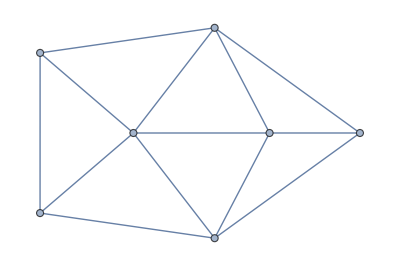

```mathematica
h
```

```mathematica
Select[Keys[allGraphs],IsomorphicGraphQ[allGraphs[#,"graph"],h]&]
```

{8047690274306,8047675926157,8894966149495,8048844564076,10594190976661,8047733498101}

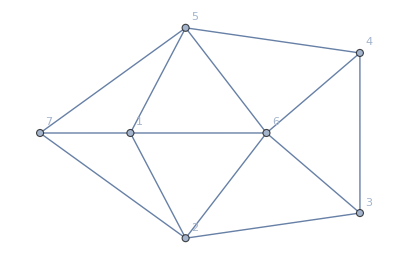
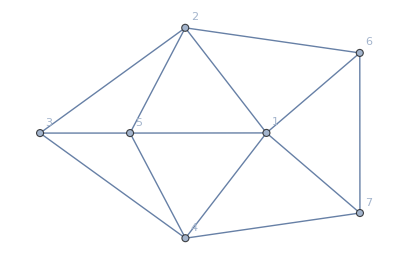
{{(2 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 2 | 1 | 0 | 0 | 1 | 1 | 1
0 | 1 | 2 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 2 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 2 | 2
1 | 1 | 0 | 0 | 1 | 0 | 2 | 2),-Graphics-},{(2 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 2 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 2 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 2 | 1 | 1 | 2
1 | 1 | 1 | 1 | 1 | 2 | 0 | 1
1 | 1 | 0 | 0 | 1 | 0 | 2 | 1
1 | 0 | 0 | 1 | 2 | 1 | 1 | 2),-Graphics-},{(2 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 2 | 1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 2 | 2 | 1 | 0 | 1
1 | 0 | 1 | 2 | 2 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 2 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 1 | 1 | 0 | 1 | 2),-Graphics-},{(2 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 1 | 1 | 0
0 | 1 | 2 | 2 | 1 | 1 | 0 | 0
0 | 1 | 2 | 2 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 2 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 2 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 2),-Graphics-},{(2 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 2 | 2 | 1 | 0 | 1 | 1 | 0
1 | 2 | 2 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 2 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 2 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 2 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 2),-Graphics-},{(2 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 2 | 1 | 0 | 0 | 1 | 2 | 1
0 | 1 | 2 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 2 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 2 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 2 | 1 | 0
1 | 2 | 1 | 0 | 0 | 1 | 2 | 1
1 | 1 | 0 | 0 | 1 | 0 | 1 | 2),-Graphics-}}

```mathematica
Table[{MatrixForm[allGraphs[k,"matrix"]],Graph[EdgeList[allGraphs[k,"graph"]],VertexLabels->"Name"]},{k,Select[Keys[allGraphs],IsomorphicGraphQ[allGraphs[#,"graph"],h]&]}]
```

```mathematica
Map[With[{g=allGraphs[#,"graph"]},{VertexCount[g],EdgeCount[g]}]&,Keys[allGraphs]]//Tally//Sort
```

{{{4,6},55},{{5,8},56},{{5,9},186},{{5,10},150},{{6,10},16},{{6,11},130},{{6,12},385},{{6,13},539},{{6,14},364},{{6,15},96},{{7,13},15},{{7,14},122},{{7,15},436},{{7,16},894},{{7,17},1150},{{7,18},950},{{7,19},492},{{7,20},146},{{7,21},19},{{8,15},1},{{8,16},13},{{8,17},78},{{8,18},286},{{8,19},715},{{8,20},1287},{{8,21},1716},{{8,22},1716},{{8,23},1287},{{8,24},715},{{8,25},286},{{8,26},78},{{8,27},13},{{8,28},1}}

```mathematica
allGraphs[8047690274306,"colofour"]/.repZero/.repcolofourgraph2
```

-Graphics-v13x24x5x67813981424317289+-Graphics-v13x25x4x67813980649476311+-Graphics-v13x25x478x613980649479215+-Graphics-v14x25x3x67812286072257425+-Graphics-v14x2x35x67812285686431259+-Graphics-v1x24x35x67811439560083283+-Graphics-v14x25x378x612286072493609

```mathematica
prob=Problems[allGraphs,{8047690274306,8047675926157,8894966149495,8048844564076,10594190976661,8047733498101}];
```

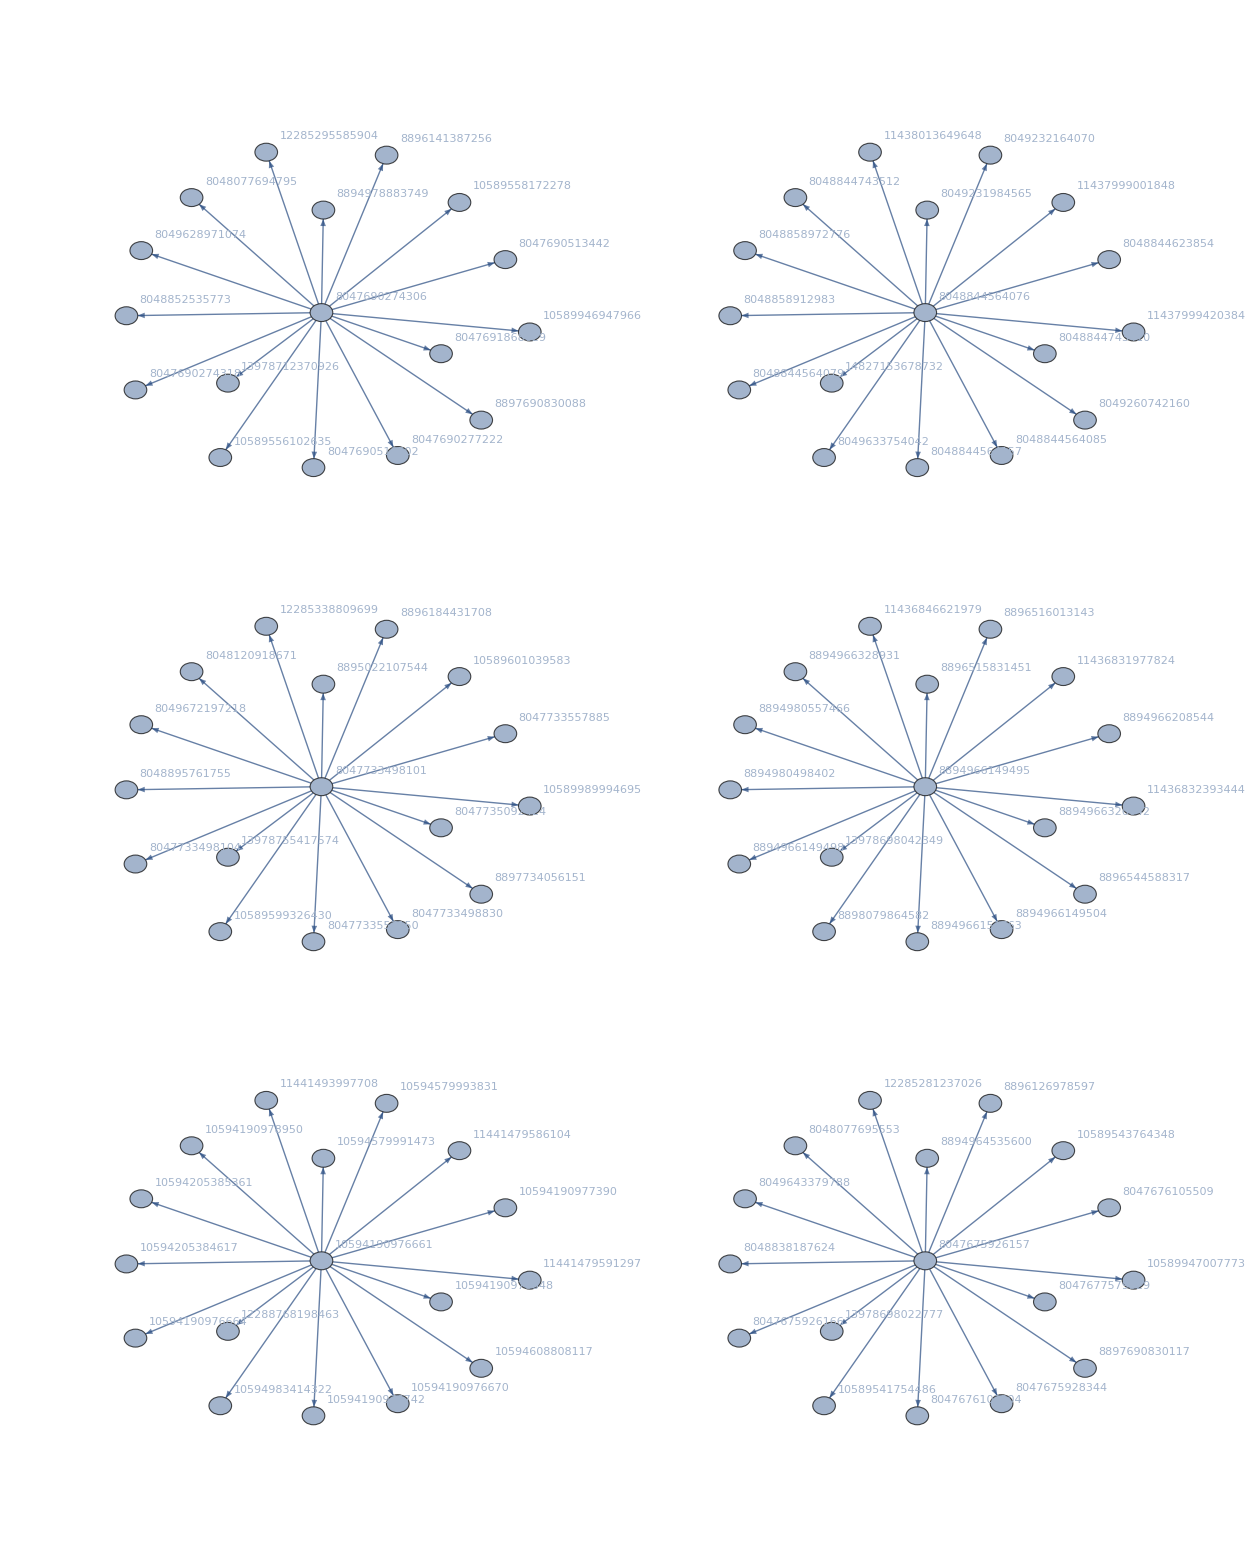

```mathematica
Graph[prob,VertexLabels->"Name"]
```

```mathematica
Table[allGraphs[k,"colofour"]/.repZero/.repcolofourgraph2,{k,{8047690274306,8047675926157,8894966149495,8048844564076,10594190976661,8047733498101}}]
```

{-Graphics-v13x24x5x67813981424317289+-Graphics-v13x25x4x67813980649476311+-Graphics-v13x25x478x613980649479215+-Graphics-v14x25x3x67812286072257425+-Graphics-v14x2x35x67812285686431259+-Graphics-v1x24x35x67811439560083283+-Graphics-v14x25x378x612286072493609,-Graphics-v13x24x58x6713981424317312+-Graphics-v13x258x4x6713980663825241+-Graphics-v13x258x47x613980663827419+-Graphics-v14x258x3x6712286086606355+-Graphics-v14x2x358x6712285686490331+-Graphics-v1x24x358x6711439560142355+-Graphics-v14x258x37x612286086783493,-Graphics-v13x245x68x713981811757451+-Graphics-v13x245x67x813981811757457+-Graphics-v13x28x45x6713980276424408+-Graphics-v13x28x457x613980276426667+-Graphics-v13x2x457x6813980262077763+-Graphics-v1x245x37x6811439946106269+-Graphics-v1x245x38x6711439945988177,-Graphics-v134x25x68x714827942868713+-Graphics-v134x25x67x814827942868719+-Graphics-v134x28x5x6714827569797137+-Graphics-v134x28x57x614827569797209+-Graphics-v134x2x57x6814827555448305+-Graphics-v1x25x347x6811438788610275+-Graphics-v1x25x348x6711438788490725,-Graphics-v14x235x68x712289560636139+-Graphics-v14x235x67x812289560636145+-Graphics-v14x238x5x6712289186029289+-Graphics-v14x238x57x612289186029361+-Graphics-v14x23x57x6812289171621408+-Graphics-v1x235x47x6811442272028883+-Graphics-v1x235x48x6711442272027431,-Graphics-v13x247x5x6813981467366187+-Graphics-v13x257x4x6813980692523103+-Graphics-v13x257x48x613980692523829+-Graphics-v14x257x3x6812286115304217+-Graphics-v1x247x35x6811439603132181+-Graphics-v14x27x35x6812285729477970+-Graphics-v14x257x38x612286115363263}

## inequalities have to be computed for 7 nodes

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsPure]
```

14393

```mathematica
ineqsPureAnd=Fold[And,ineqsPure];
```

We can remove any eqaution of the for x1+x2 +... >=0 since that doesn’t really add any information

```mathematica
trivial=Length[Select[ineqsPure,Length[#[[1]]]≠1&&#[[0]]==GreaterEqual&]]
```

5113

```mathematica
interestingPure=Select[ineqsPure,Length[#[[1]]]==1||ToString[#[[0]]]≠"GreaterEqual"&];Length[interestingPure]
```

9280

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsPure,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]];Length[repZero]
```

266

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
atomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,atomKeys}];Length[atomFacts]
```

321

```mathematica
assocComp=Association[];Table[assocComp[allGraphs[k,"colofour"]]=If[ToString[allGraphs[k,"comp"]]=="GreaterEqual",1,0],{k,atomKeys}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1}

```mathematica
ExpWeight[exp_]:=Product[assocComp[var],{var,ListofVars[exp]}]
```

```mathematica
interestingPureAnd=Fold[And,interestingPure];
```

```mathematica
simplifiedPure=Monitor[Simplify[interestingPureAnd,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->atomFacts],countDone];Length[simplifiedPure]
```

6

```mathematica
ListofVars[simplifiedPure]//DeleteDuplicates//Length
```

42

```mathematica
simplifiedPure
```

v13x24x5x678+v13x25x478x6+v13x25x4x678+v14x25x378x6+v14x25x3x678+v14x2x35x678+v1x24x35x678>0&&v13x24x58x67+v13x258x47x6+v13x258x4x67+v14x258x37x6+v14x258x3x67+v14x2x358x67+v1x24x358x67>0&&v13x245x67x8+v13x245x68x7+v13x28x457x6+v13x28x45x67+v13x2x457x68+v1x245x37x68+v1x245x38x67>0&&v134x25x67x8+v134x25x68x7+v134x28x57x6+v134x28x5x67+v134x2x57x68+v1x25x347x68+v1x25x348x67>0&&v14x235x67x8+v14x235x68x7+v14x238x57x6+v14x238x5x67+v14x23x57x68+v1x235x47x68+v1x235x48x67>0&&v13x247x5x68+v13x257x48x6+v13x257x4x68+v14x257x38x6+v14x257x3x68+v14x27x35x68+v1x247x35x68>0

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[#]&,AndToTable[simplifiedPure]]]]//Sort
```

{v134x25x67x8,v134x25x68x7,v134x28x57x6,v134x28x5x67,v134x2x57x68,v13x245x67x8,v13x245x68x7,v13x247x5x68,v13x24x58x67,v13x24x5x678,v13x257x48x6,v13x257x4x68,v13x258x47x6,v13x258x4x67,v13x25x478x6,v13x25x4x678,v13x28x457x6,v13x28x45x67,v13x2x457x68,v14x235x67x8,v14x235x68x7,v14x238x57x6,v14x238x5x67,v14x23x57x68,v14x257x38x6,v14x257x3x68,v14x258x37x6,v14x258x3x67,v14x25x378x6,v14x25x3x678,v14x27x35x68,v14x2x358x67,v14x2x35x678,v1x235x47x68,v1x235x48x67,v1x245x37x68,v1x245x38x67,v1x247x35x68,v1x24x358x67,v1x24x35x678,v1x25x347x68,v1x25x348x67}

```mathematica
simplifiedPureTable=AndToTable[simplifiedPure];
```

```mathematica
Take[simplifiedPure,1]/.repcolofourtextBase2
```

v13x24x5x678+v13x25x478x6+v13x25x4x678+v14x25x378x6+v14x25x3x678+v14x2x35x678+v1x24x35x678>0

```mathematica
Select[Keys[allGraphs],MemberQ[ListofVars[allGraphs[#,"colofour"]],v13x25x4x6x7]&]
```

{}

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[allGraphs[#,"colofour"]]&,Keys[allGraphs]]]]//Sort
```

{v146x257x3,v146x25x37,v146x25x3x7,v146x27x3x5,v146x2x37x5,v146x2x3x57,v146x2x3x5x7,v14x257x36,v14x257x3x6,v14x25x36x7,v14x25x37x6,v14x25x3x6x7,v14x26x37x5,v14x26x3x57,v14x26x3x5x7,v14x27x36x5,v14x27x3x5x6,v14x2x36x57,v14x2x36x5x7,v14x2x37x5x6,v14x2x3x57x6,v14x2x3x5x6x7,v15x246x37,v15x246x3x7,v15x247x36,v15x247x3x6,v15x24x36x7,v15x24x37x6,v15x24x3x6x7,v15x26x37x4,v15x26x3x47,v15x26x3x4x7,v15x27x36x4,v15x27x3x46,v15x27x3x4x6,v15x2x36x47,v15x2x36x4x7,v15x2x37x46,v15x2x37x4x6,v15x2x3x46x7,v15x2x3x47x6,v15x2x3x4x6x7,v16x247x3x5,v16x24x37x5,v16x24x3x57,v16x24x3x5x7,v16x257x3x4,v16x25x37x4,v16x25x3x47,v16x25x3x4x7,v16x27x3x4x5,v16x2x37x4x5,v16x2x3x47x5,v16x2x3x4x57,v16x2x3x4x5x7,v1x246x37x5,v1x246x3x57,v1x246x3x5x7,v1x247x36x5,v1x247x3x5x6,v1x24x36x57,v1x24x36x5x7,v1x24x37x5x6,v1x24x3x57x6,v1x24x3x5x6x7,v1x257x36x4,v1x257x3x46,v1x257x3x4x6,v1x25x36x47,v1x25x36x4x7,v1x25x37x46,v1x25x37x4x6,v1x25x3x46x7,v1x25x3x47x6,v1x25x3x4x6x7,v1x26x37x4x5,v1x26x3x47x5,v1x26x3x4x57,v1x26x3x4x5x7,v1x27x36x4x5,v1x27x3x46x5,v1x27x3x4x5x6,v1x2x36x47x5,v1x2x36x4x57,v1x2x36x4x5x7,v1x2x37x46x5,v1x2x37x4x5x6,v1x2x3x46x57,v1x2x3x46x5x7,v1x2x3x47x5x6,v1x2x3x4x57x6,v1x2x3x4x5x6x7}

```mathematica
ExpressionToTable[simplifiedPureTable]/.repcolofourtextBase2
```

v13x24x5x678+v13x25x478x6+v13x25x4x678+v14x25x378x6+v14x25x3x678+v14x2x35x678+v1x24x35x678>0
v13x24x58x67+v13x258x47x6+v13x258x4x67+v14x258x37x6+v14x258x3x67+v14x2x358x67+v1x24x358x67>0
v134x25x67x8+v134x25x68x7+v134x28x57x6+v134x28x5x67+v134x2x57x68+v1x25x347x68+v1x25x348x67>0
v13x245x67x8+v13x245x68x7+v13x28x457x6+v13x28x45x67+v13x2x457x68+v1x245x37x68+v1x245x38x67>0
v14x235x67x8+v14x235x68x7+v14x238x57x6+v14x238x5x67+v14x23x57x68+v1x235x47x68+v1x235x48x67>0
v13x247x5x68+v13x257x48x6+v13x257x4x68+v14x257x38x6+v14x257x3x68+v14x27x35x68+v1x247x35x68>0

```mathematica
Length[expList]
```

63

```mathematica
Graph[ExpressionsToGraph6[simple],ImageSize->1200]
```

## Time to go for the pentagon

We set all pentagons to zero :

```mathematica
Monitor[
Table[
With[{
mat2=ContractNodes[mat,nodes]
},
Print[Timing[Monitor[ComputeGraph[mat2,32],{globalDepth,Length[allGraphs]}]]];
With[{key=GraphMatrixSignature[mat2]},
allGraphs[key,"comp"]=Equal;
allGraphs[key,"compwhy"]="In terminis"
]
]
,
{nodes,{{7,8,1},{3,4,6}}}
],
nodes]
```

{11.8281,8089531687130}

{11.6719,11437999539850}

{In terminis,In terminis}

```mathematica
PushAllGraphs[]
```

The parent x8089531687130 is zero (so this must be ==0)

The parent x8089531687130 is zero (so this must be ==0)

The parent x8089531687130 is zero (so this must be ==0)

«7 more identical outputs»

The parent x10631397751655 is zero (so this must be ==0)

The parent x10631397751655 is zero (so this must be ==0)

The parent x10631397751655 is zero (so this must be ==0)

«3 more identical outputs»

The parent x11478686364014 is zero (so this must be ==0)

The parent x11478686364014 is zero (so this must be ==0)

The parent x11481398307437 is zero (so this must be ==0)

The parent x12327137237840 is zero (so this must be ==0)

The parent x12327137237840 is zero (so this must be ==0)

The parent x12327137237840 is zero (so this must be ==0)

«1 more identical outputs»

The parent x10632560013122 is zero (so this must be ==0)

The parent x10632560013122 is zero (so this must be ==0)

The parent x10632560013122 is zero (so this must be ==0)

The parent x14020554022862 is zero (so this must be ==0)

The parent x14020554022862 is zero (so this must be ==0)

The parent x14020554022862 is zero (so this must be ==0)

«1 more identical outputs»

The parent x8936820299489 is zero (so this must be ==0)

The parent x8936820299489 is zero (so this must be ==0)

The parent x8936820299489 is zero (so this must be ==0)

«1 more identical outputs»

The parent x8937982560956 is zero (so this must be ==0)

The parent x8939532242912 is zero (so this must be ==0)

The parent x8937207719978 is zero (so this must be ==0)

The parent x8090693948597 is zero (so this must be ==0)

The parent x8090693948597 is zero (so this must be ==0)

The parent x8089919107619 is zero (so this must be ==0)

The parent x11437999539850 is zero (so this must be ==0)

The parent x11437999539850 is zero (so this must be ==0)

The parent x11437999539850 is zero (so this must be ==0)

«7 more identical outputs»

The parent x11438386960339 is zero (so this must be ==0)

The parent x11438386960339 is zero (so this must be ==0)

The parent x11438386960339 is zero (so this must be ==0)

«3 more identical outputs»

The parent x11438401309246 is zero (so this must be ==0)

The parent x11438401309246 is zero (so this must be ==0)

The parent x11438401608151 is zero (so this must be ==0)

The parent x11438415717934 is zero (so this must be ==0)

The parent x11438415717934 is zero (so this must be ==0)

The parent x11438415717934 is zero (so this must be ==0)

«1 more identical outputs»

The parent x11438387139682 is zero (so this must be ==0)

The parent x11438387199463 is zero (so this must be ==0)

The parent x11438387020120 is zero (so this must be ==0)

The parent x11438788729816 is zero (so this must be ==0)

The parent x11438788729816 is zero (so this must be ==0)

The parent x11438788729816 is zero (so this must be ==0)

«1 more identical outputs»

The parent x11438013888757 is zero (so this must be ==0)

The parent x11438013888757 is zero (so this must be ==0)

The parent x11438013888757 is zero (so this must be ==0)

«1 more identical outputs»

The parent x11438014068100 is zero (so this must be ==0)

The parent x11438014187662 is zero (so this must be ==0)

The parent x11438013948538 is zero (so this must be ==0)

The parent x11437999719193 is zero (so this must be ==0)

The parent x11437999719193 is zero (so this must be ==0)

The parent x11437999599631 is zero (so this must be ==0)

80

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

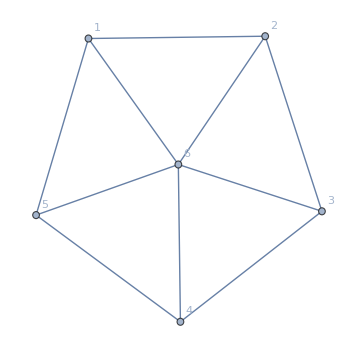

```mathematica
Graph[EdgeList[allGraphs[8089531687130,"graph"]],VertexLabels->"Name"]
```

```mathematica
allGraphs[11437999539850,"colofour"]/.repcolofourgraph2
```

-Graphics-v1x25x3468x711438789028721+-Graphics-v1x25x3467x811438789148283+-Graphics-v1x28x346x5711438415897439+-Graphics-v1x28x3467x511438416076701+-Graphics-v1x2x3468x5711438401608313+-Graphics-v1x25x346x7x811438788968940+-Graphics-v1x28x346x5x711438415897358+-Graphics-v1x2x3468x5x711438401608232+-Graphics-v1x2x346x57x811438401548532+-Graphics-v1x2x3467x5x811438401727794+-Graphics-v1x2x346x5x7x811438401548451

## inequalities have to be re-computed

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsPure]
```

14507

```mathematica
ineqsPureAnd=Fold[And,ineqsPure];
```

We can remove any eqaution of the for x1+x2 +... >=0 since that doesn’t really add any information

```mathematica
trivial=Length[Select[ineqsPure,Length[#[[1]]]≠1&&#[[0]]==GreaterEqual&]]
```

5113

```mathematica
interestingPure=Select[ineqsPure,Length[#[[1]]]==1||ToString[#[[0]]]≠"GreaterEqual"&];Length[interestingPure]
```

9394

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsPure,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]];Length[repZero]
```

288

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
atomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,atomKeys}];Length[atomFacts]
```

343

```mathematica
assocComp=Association[];Table[assocComp[allGraphs[k,"colofour"]]=If[ToString[allGraphs[k,"comp"]]=="GreaterEqual",1,0],{k,atomKeys}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ExpWeight[exp_]:=Product[assocComp[var],{var,ListofVars[exp]}]
```

```mathematica
interestingPureAnd=Fold[And,interestingPure];
```

```mathematica
simplifiedPure=Monitor[Simplify[interestingPureAnd,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->atomFacts],countDone];Length[simplifiedPure]
```

6

```mathematica
ListofVars[simplifiedPure]//DeleteDuplicates//Length
```

42

```mathematica
simplifiedPure
```

v13x24x5x678+v13x25x478x6+v13x25x4x678+v14x25x378x6+v14x25x3x678+v14x2x35x678+v1x24x35x678>0&&v13x24x58x67+v13x258x47x6+v13x258x4x67+v14x258x37x6+v14x258x3x67+v14x2x358x67+v1x24x358x67>0&&v13x245x67x8+v13x245x68x7+v13x28x457x6+v13x28x45x67+v13x2x457x68+v1x245x37x68+v1x245x38x67>0&&v134x25x67x8+v134x25x68x7+v134x28x57x6+v134x28x5x67+v134x2x57x68+v1x25x347x68+v1x25x348x67>0&&v14x235x67x8+v14x235x68x7+v14x238x57x6+v14x238x5x67+v14x23x57x68+v1x235x47x68+v1x235x48x67>0&&v13x247x5x68+v13x257x48x6+v13x257x4x68+v14x257x38x6+v14x257x3x68+v14x27x35x68+v1x247x35x68>0

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[#]&,AndToTable[simplifiedPure]]]]//Sort
```

{v134x25x67x8,v134x25x68x7,v134x28x57x6,v134x28x5x67,v134x2x57x68,v13x245x67x8,v13x245x68x7,v13x247x5x68,v13x24x58x67,v13x24x5x678,v13x257x48x6,v13x257x4x68,v13x258x47x6,v13x258x4x67,v13x25x478x6,v13x25x4x678,v13x28x457x6,v13x28x45x67,v13x2x457x68,v14x235x67x8,v14x235x68x7,v14x238x57x6,v14x238x5x67,v14x23x57x68,v14x257x38x6,v14x257x3x68,v14x258x37x6,v14x258x3x67,v14x25x378x6,v14x25x3x678,v14x27x35x68,v14x2x358x67,v14x2x35x678,v1x235x47x68,v1x235x48x67,v1x245x37x68,v1x245x38x67,v1x247x35x68,v1x24x358x67,v1x24x35x678,v1x25x347x68,v1x25x348x67}

```mathematica
simplifiedPureTable=AndToTable[simplifiedPure];
```

```mathematica
Take[simplifiedPure,1]/.repcolofourtextBase2
```

v13x24x5x678+v13x25x478x6+v13x25x4x678+v14x25x378x6+v14x25x3x678+v14x2x35x678+v1x24x35x678>0

```mathematica
Select[Keys[allGraphs],MemberQ[ListofVars[allGraphs[#,"colofour"]],v13x25x4x6x7]&]
```

{}

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[allGraphs[#,"colofour"]]&,Keys[allGraphs]]]]//Sort
```

{v146x257x3,v146x25x37,v146x25x3x7,v146x27x3x5,v146x2x37x5,v146x2x3x57,v146x2x3x5x7,v14x257x36,v14x257x3x6,v14x25x36x7,v14x25x37x6,v14x25x3x6x7,v14x26x37x5,v14x26x3x57,v14x26x3x5x7,v14x27x36x5,v14x27x3x5x6,v14x2x36x57,v14x2x36x5x7,v14x2x37x5x6,v14x2x3x57x6,v14x2x3x5x6x7,v15x246x37,v15x246x3x7,v15x247x36,v15x247x3x6,v15x24x36x7,v15x24x37x6,v15x24x3x6x7,v15x26x37x4,v15x26x3x47,v15x26x3x4x7,v15x27x36x4,v15x27x3x46,v15x27x3x4x6,v15x2x36x47,v15x2x36x4x7,v15x2x37x46,v15x2x37x4x6,v15x2x3x46x7,v15x2x3x47x6,v15x2x3x4x6x7,v16x247x3x5,v16x24x37x5,v16x24x3x57,v16x24x3x5x7,v16x257x3x4,v16x25x37x4,v16x25x3x47,v16x25x3x4x7,v16x27x3x4x5,v16x2x37x4x5,v16x2x3x47x5,v16x2x3x4x57,v16x2x3x4x5x7,v1x246x37x5,v1x246x3x57,v1x246x3x5x7,v1x247x36x5,v1x247x3x5x6,v1x24x36x57,v1x24x36x5x7,v1x24x37x5x6,v1x24x3x57x6,v1x24x3x5x6x7,v1x257x36x4,v1x257x3x46,v1x257x3x4x6,v1x25x36x47,v1x25x36x4x7,v1x25x37x46,v1x25x37x4x6,v1x25x3x46x7,v1x25x3x47x6,v1x25x3x4x6x7,v1x26x37x4x5,v1x26x3x47x5,v1x26x3x4x57,v1x26x3x4x5x7,v1x27x36x4x5,v1x27x3x46x5,v1x27x3x4x5x6,v1x2x36x47x5,v1x2x36x4x57,v1x2x36x4x5x7,v1x2x37x46x5,v1x2x37x4x5x6,v1x2x3x46x57,v1x2x3x46x5x7,v1x2x3x47x5x6,v1x2x3x4x57x6,v1x2x3x4x5x6x7}

```mathematica
ExpressionToTable[simplifiedPureTable]/.repcolofourtextBase2
```

v13x24x5x678+v13x25x478x6+v13x25x4x678+v14x25x378x6+v14x25x3x678+v14x2x35x678+v1x24x35x678>0
v13x24x58x67+v13x258x47x6+v13x258x4x67+v14x258x37x6+v14x258x3x67+v14x2x358x67+v1x24x358x67>0
v134x25x67x8+v134x25x68x7+v134x28x57x6+v134x28x5x67+v134x2x57x68+v1x25x347x68+v1x25x348x67>0
v13x245x67x8+v13x245x68x7+v13x28x457x6+v13x28x45x67+v13x2x457x68+v1x245x37x68+v1x245x38x67>0
v14x235x67x8+v14x235x68x7+v14x238x57x6+v14x238x5x67+v14x23x57x68+v1x235x47x68+v1x235x48x67>0
v13x247x5x68+v13x257x48x6+v13x257x4x68+v14x257x38x6+v14x257x3x68+v14x27x35x68+v1x247x35x68>0

```mathematica
Length[expList]
```

63

```mathematica
Graph[ExpressionsToGraph6[simple],ImageSize->1200]
```